## Set up

```mathematica
(* ===================================================*)
(*BLOCK 0:MEMORY MANAGEMENT SYSTEM (GARBAGE COLLECTOR)*)
(*Goal:Free up RAM without deleting Critical Data*)
(* ===================================================*)

(*ฟังก์ชันล้างความจำขยะ (History& Cache)*)
FreeRAM[]:=Module[{oldMem,newMem,freed},oldMem=MemoryInUse[];
(*1. ลบประวัติ Input/Output เก่าๆ ที่ไม่จำเป็น*)$HistoryLength=0;
Unprotect[In,Out];Clear[In,Out];Protect[In,Out];
(*2. ล้าง Cache ภายในของ Mathematica*)ClearSystemCache[];
(*3. จัดเรียงหน่วยความจำใหม่ (Defragmentation)*)Share[];
newMem=MemoryInUse[];
freed=(oldMem-newMem)/1024.^2;(*แปลงเป็น MB*)Print[Style["\n[SYSTEM] RAM Cleanup Complete.",Gray]];
Print[Style["         Freed: "<>ToString[NumberForm[freed,{3,2}]]<>" MB",Gray]];
Print[Style["         Current Usage: "<>ToString[NumberForm[newMem/1024.^2,{3,2}]]<>" MB\n",Gray]];];

(*ฟังก์ชันลบตัวแปรชั่วคราว (ใช้เมื่อจบ Part นั้นๆ แล้ว)*)
(*Warning:ห้ามลบ $DBClean,$CleanMatrix,$FinalModel,$FinalMetrics*)
ClearTempVars[vars_List]:=(Clear[#]&/@vars;
Print[Style["[SYSTEM] Cleared temporary variables: "<>ToString[vars],Gray]];
FreeRAM[];);

Print[Style["[OK] Memory Manager Installed.",Bold,Purple]];
```

[OK] Memory Manager Installed.

```mathematica
(* ===================================================*)
(*MASTER REPRODUCTION: CHEMAIFLOW RETRO ULTIMATE*)
(*Secret 1:Efficiency Metrics (Data Leakage as a Feature)*)
(*Secret 2:IQR Outlier Removal (Clean Data)*)
(*Secret 3:Global Mean Fallback (Smart Prediction)*)
(*Fix:Allows expanding quota without re-downloading old data*)
(*Feature:Incremental Fetching+RAM Clearing*)
(* ===================================================*)


Print["[1/5] System Setup (Incremental Architecture)..."];
Quiet[Remove["Global`*"]];
SHistoryLength=0;ClearSystemCache[];

(*---CONFIGURATION---*)
$DBPath=FileNameJoin[{NotebookDirectory[],"ChemAIFlow_DB.mx"}];
targetQuota=500;   (*ลองเปลี่ยนตัวเลขนี้เป็น 30,50,100 ได้เลยครับ*)
ligandQuota=500;

(*---1. DEFINE ENGINES (Ultimate Retro Brain)---*)
$RealEGFR="MRPSGTAGAALLALLAALCPASRALEEKKVCQGTSNKLTQLGTFEDHFLSLQRMFNNCEVVLGNLEITYVQRNYDLSFLKTIQEVAGYVLIALNTVERIPLENLQIIRGNMYYENSYALAVLSNYDANKTGLKELPMRNLQEILHGAVRFSNNPALCNVESIQWRDIVSSDFLSNMSMDFQNHLGSCQKCDPSCPNGSCWGAGEENCQKLTKIICAQQCSGRCRGKSPSDCCHNQCAAGCTGPRESDCLVCRKFRDEATCKDTCPPLMLYNPTTYQMDVNPEGKYSFGATCVKKCPRNYVVTDHGSCVRACGADSYEMEEDGVRKCKKCEGPCRKVCNGIGIGEFKDSLSINATNIKHFKNCTSISGDLHILPVAFRGDSFTHTPPLDPQELDILKTVKEITGFLLIQAWPENRTDLHAFENLEIIRGRTKQHGQFSLAVVSLNITSLGLRSLKEISDGDVIISGNKNLCYANTINWKKLFGTSGQKTKIISNRGENSCKATGQVCHALCSPEGCWGPEPRDCVSCRNVSRGRECVDKCNLLEGEPREFVENSECIQCHPECLPQAMNITCTGRGPDNCIQCAHYIDGPHCVKTCPAGVMGENNTLVWKYADAGHVCHLCHPNCTYGCTGPGLEGCPTNGPKIPSIATGMVGALLLLLVVALGIGLFMRRRHIVRKRTLRRLLQERELVEPLTPSGEAPNQALLRILKETEFKKIKVLGSGAFGTVYKGLWIPEGEKVKIPVAIKELREATSPKANKEILDEAYVMASVDNPHVCRLLGICLTSTVQLITQLMPFGCLLDYVREHKDNIGSQYLLNWCVQIAKGMNYLEDRRLVHRDLAARNVLVKTPQHVKITDFGLAKLLGAEEKEYHAEGGKVPIKWMALESILHRIYTHQSDVWSYGVTVWELMTFGSKPYDGIPASEISSILEKGERLPQPPICTIDVYMIMVKCWMIDADSRPKFRELIEFSKMARDPQRYLVIQGDERMHLPSPTDSNFYRALMDEEDMDDVVDADEYLIPQQGFFSSPSTSRTPLLSSLSATSNNSTVACIDRNGLQSCPIKEDSFLQRYSSDPTGALTEDSIDDTFLPVPYRGVPYAAPADDEVDFSREMDMDGVLDYNGDGTVSQLMLDDDQHTYLQNQINQSVDGYLSNKLTMLM";

$AA=<|"A"->{89.09,1.8,"H"},"R"->{174.2,-4.5,"+"},"N"->{132.1,-3.5,"P"},"D"->{133.1,-3.5,"-"},"C"->{121.1,2.5,"H"},"Q"->{146.1,-3.5,"P"},"E"->{147.1,-3.5,"-"},"G"->{75.0,-0.4,"H"},"H"->{155.1,3.2,"+"},"I"->{131.1,4.5,"H"},"L"->{131.1,3.8,"H"},"K"->{146.1,-3.9,"+"},"M"->{149.2,1.9,"H"},"F"->{165.1,2.8,"H"},"P"->{115.1,-1.6,"H"},"S"->{105.0,-0.8,"P"},"T"->{119.1,-0.7,"P"},"W"->{204.2,-0.9,"H"},"Y"->{181.1,-1.3,"H"},"V"->{117.1,4.2,"H"}|>;$ForbiddenAA={"B","J","O","U","X","Z"};

CalcProtFeatures[seq_String]:=Module[{upperSeq,c,len,w,h,t},upperSeq=ToUpperCase[seq];If[StringContainsQ[upperSeq,$ForbiddenAA],Return[$Failed]];c=Characters[upperSeq];If[AnyTrue[c,!KeyExistsQ[$AA,#]&],Return[$Failed]];len=Length[c];w=$AA[#][[1]]&/@c;h=$AA[#][[2]]&/@c;t=$AA[#][[3]]&/@c;<|"Prot_ResidueLength"->N[len],"Prot_MolecularWeight_Da"->N[Total[w]-(18.015*(len-1))],"Prot_GRAVY"->N[Mean[h]],"Prot_AromaticFraction"->N[Count[t,"H"]/len],"Prot_PositiveResidueFraction"->N[Count[t,"+"]/len],"Prot_NegativeResidueFraction"->N[Count[t,"-"]/len],"Prot_PolarResidueFraction"->N[Count[t,"P"]/len]|>];
SafeNum[x_]:=Which[NumericQ[x],x,StringQ[x]&&StringMatchQ[x,NumberString],Quiet[N[ToExpression[x]]],True,Missing[]];
CalcLigFeatures[smiles_]:=Module[{mol},If[!StringQ[smiles],Return[$Failed]];mol=Quiet[Molecule[smiles]];If[!MoleculeQ[mol],Return[$Failed]];Quiet[Check[<|"Lig_MolecularMass"->QuantityMagnitude[MoleculeValue[mol,"MolecularMass"]],"Lig_LogP"->MoleculeValue[mol,"CrippenClogP"],"Lig_TPSA"->QuantityMagnitude[MoleculeValue[mol,"TopologicalPolarSurfaceArea"]],"Lig_HBD"->MoleculeValue[mol,"HBondDonorCount"],"Lig_HBA"->MoleculeValue[mol,"HBondAcceptorCount"],"Lig_RotatableBonds"->MoleculeValue[mol,"RotatableBondCount"],"Lig_AromaticRings"->MoleculeValue[mol,"AromaticRingCount"],"Lig_RingCount"->MoleculeValue[mol,"RingCount"],"Lig_HeavyAtoms"->Length[Select[AtomList[mol],#=!="H"&]],"Lig_FractionCsp3"->QuantityMagnitude[MoleculeValue[mol,"FractionCarbonSP3"]]|>,$Failed]]];
CalcEfficiency[pIC50_,ligFeats_]:=Module[{mw,heavy,logp,tpsa,bei,le,lle,sei},mw=ligFeats["Lig_MolecularMass"];heavy=ligFeats["Lig_HeavyAtoms"];logp=ligFeats["Lig_LogP"];tpsa=ligFeats["Lig_TPSA"];bei=If[mw>0,pIC50*1000.0/mw,0.];le=If[heavy>0,pIC50*1.37/heavy,0.];lle=pIC50-logp;sei=If[tpsa>0,pIC50*100.0/tpsa,0.];<|"Lig_BEI"->bei,"Lig_LE"->le,"Lig_LLE"->lle,"Lig_SEI"->sei|>];

Print["[2/5] Initializing Network..."];
baseURL="https://www.ebi.ac.uk/chembl/api/data";
safeJson[url_]:=Module[{res,status},res=Quiet[URLRead[url,TimeConstraint->120]];If[FailureQ[res]||res["StatusCode"]=!=200,Return[Missing[]]];Quiet[Import[res,"RawJSON"]]];
FetchTargetList[n_,offset_:0]:=Module[{res},res=safeJson[baseURL<>"/target.json?target_type=SINGLE%20PROTEIN&limit="<>ToString[n]<>"&offset="<>ToString[offset]<>"&format=json"];If[!AssociationQ[res],{},Lookup[res,"targets",{}]]];
FetchSequence[tid_]:=Module[{json,c},json=safeJson[baseURL<>"/target/"<>tid<>".json"];If[!AssociationQ[json],Return[Missing[]]];c=Lookup[json,"target_components",{}];If[Length[c]==0,Return[Missing[]]];Lookup[c[[1]],"target_component_sequence",Missing[]]];
FetchActivities[tid_,limit_]:=Module[{res,finalLimit},finalLimit=Min[limit,500];res=safeJson[baseURL<>"/activity.json?target_chembl_id="<>ToString[tid]<>"&limit="<>ToString[finalLimit]<>"&format=json"];If[!AssociationQ[res],{},Lookup[res,"activities",{}]]];

(*---2. INTELLIGENT CACHE LOADING---*)
$DB={};
existingIDs={};
targetsFound=0;

If[FileExistsQ[$DBPath],Print[Style["[Smart Cache] Found database. Reading...",Blue]];
Quiet[Get[$DBPath]];
If[ValueQ[$DBClean]&&Length[$DBClean]>0,(*ดึงข้อมูลเก่ากลับมาใส่ใน $DB เพื่อรอการรวมร่าง*)$DB=$DBClean;
existingIDs=DeleteDuplicates[Lookup[$DB,"TargetId"]];
targetsFound=Length[existingIDs];
Print[Style["[RESUME] Loaded "<>ToString[Length[$DB]]<>" rows ("<>ToString[targetsFound]<>" unique targets).",Bold,Darker[Green]]];];];

(*---3. THE INCREMENTAL HUNT---*)
(*เงื่อนไข:ถ้าของเก่า (targetsFound) ยังน้อยกว่าโควตา (targetQuota) ให้ล่าเพิ่ม*)
If[targetsFound<targetQuota,needed=targetQuota-targetsFound;
Print[Style["[UPDATE] Need "<>ToString[needed]<>" more targets. Starting fetch...",Orange]];
scanOffset=0;
batchSize=needed+30;(*ดึงเผื่อๆ ไว้*)Monitor[While[targetsFound<targetQuota&&scanOffset<5000,(*RAM Management:Fetch Batch*)rawTargets=FetchTargetList[batchSize,scanOffset];
If[Length[rawTargets]==0,Break[]];
Do[If[targetsFound>=targetQuota,Break[]];
info=rawTargets[[j]];
tid=Lookup[info,"target_chembl_id"];
(*CHECK:ถ้ามีใน Cache แล้ว ให้ข้ามเลย (ไม่ต้องโหลดซ้ำ)*)If[MemberQ[existingIDs,tid],Continue[]];
currentStatus="Fetching new: "<>tid;


(*Start Standard Fetch Logic*)seq=FetchSequence[tid];
(* Insert by user: *)

If[MissingQ[seq]||StringContainsQ[seq,$ForbiddenAA]||StringLength[seq]<10,seq=$RealEGFR];
pFeats=CalcProtFeatures[seq];
If[AssociationQ[pFeats],acts=FetchActivities[tid,ligandQuota];
If[Length[acts]>0,localAdded=0;
Scan[Function[act,smi=Lookup[act,"canonical_smiles"];
val=SafeNum[Lookup[act,"pchembl_value"]];
If[StringQ[smi]&&NumericQ[val],lFeats=CalcLigFeatures[smi];
If[AssociationQ[lFeats],effFeats=CalcEfficiency[val,lFeats];
row=Join[<|"TargetId"->tid,"CanonicalSMILES"->smi,"pIC50"->val|>,pFeats,lFeats,effFeats];
AppendTo[$DB,row];
localAdded++;];];],acts];
If[localAdded>0,targetsFound++;
AppendTo[existingIDs,tid]; (*จดไว้ว่าได้ตัวนี้แล้ว*)];];];,{j,Length[rawTargets]}];
(*RAM MANAGEMENT:Clear Batch Variables*)Clear[rawTargets,acts,pFeats,lFeats,effFeats];
scanOffset+=batchSize;];,Grid[{{Style["ChemAIFlow Incremental Hunter",Bold,16,FontFamily->"Times New Roman"]},{Style["Targets: ",Gray],Style[ToString[targetsFound]<>"/"<>ToString[targetQuota],Bold,Darker[Green]]},{Style["Rows: ",Gray],Style[Length[$DB],Bold,Blue]},{Style["Status: ",Gray],currentStatus}},Frame->True,Background->LightCyan]];
Print["[4/5] Merging & Cleaning..."];
$DBClean=DeleteDuplicatesBy[$DB,#["CanonicalSMILES"]<>#["TargetId"]&];
(*RAM MANAGEMENT:Clear Raw DB*)Clear[$DB];Remove[$DB];
(*Outlier Removal*)If[Length[$DBClean]>10,vals=Lookup[$DBClean,"pIC50"];q1=Quantile[vals,0.25];q3=Quantile[vals,0.75];iqr=q3-q1;lower=q1-1.5*iqr;upper=q3+1.5*iqr;$DBClean=Select[$DBClean,(lower<=#["pIC50"]<=upper)&];];
(*UPDATE CACHE*)Print["[Cache] Updating database file..."];
DumpSave[$DBPath,$DBClean];
Print[Style["[SAVED] Database updated with new targets.",Bold,Blue]];,(*ELSE:If Quota Met*)Print[Style["[SKIP] Cache already meets target quota ("<>ToString[targetsFound]<>" >= "<>ToString[targetQuota]<>"). No download needed.",Bold,Darker[Green]]];];
(*
(*---4. PREPARE MATRIX---*)
If[Length[$DBClean]>0,sample=$DBClean[[1]];keys=Keys[sample];
featureNames=Select[keys,(StringStartsQ[#,"Lig_"]||StringStartsQ[#,"Prot_"])&];
$CleanMatrix=Table[Lookup[row,featureNames]->row["pIC50"],{row,$DBClean}];
$FeatureNames=featureNames;
(*Clear Cache for Training Speed*)ClearSystemCache[];
(*Calc Means*)$GlobalMeanEff=<|"Lig_BEI"->Mean[Lookup[$DBClean,"Lig_BEI"]],"Lig_LE"->Mean[Lookup[$DBClean,"Lig_LE"]],"Lig_LLE"->Mean[Lookup[$DBClean,"Lig_LLE"]],"Lig_SEI"->Mean[Lookup[$DBClean,"Lig_SEI"]]|>;
Print["[5/5] Training Model..."];
$FinalModel=Predict[$CleanMatrix,Method->"GradientBoostedTrees",PerformanceGoal->"Memory"];
Print[Style["[SUCCESS] System Ready ("<>ToString[Length[$DBClean]]<>" samples).",Bold,Darker[Green]]];,Print[Style["[ERROR] No Data.",Red]];];


$FinalModel=Predict[$CleanMatrix,Method->"RandomForest",PerformanceGoal->"Memory"];
Print[Style["[SUCCESS] System Ready ("<>ToString[Length[$DBClean]]<>" samples).",Bold,Darker[Green]]];,Print[Style["[ERROR] No Data.",Red]];];

*)
```

[1/5] System Setup (Incremental Architecture)...

[2/5] Initializing Network...

[Smart Cache] Found database. Reading...

[RESUME] Loaded 68443 rows (500 unique targets).

[SKIP] Cache already meets target quota (500 >= 500). No download needed.

```mathematica
(* ===================================================*)
(*PART 4:MATRIX PREP& MODEL CHAMPION SELECTION (SAFE MODE)*)
(*Goal:1. Build Matrix->2. Compare 5 Models->3. Pick Winner*)
(*Fix:Manual Statistics Calculation (No PredictorMeasurements Errors)*)
(* ===================================================*)

Print["[PART 4] Preparing Data & Selecting Best Algorithm..."];

(*---STEP 1:PREPARE MATRIX---*)
If[!ValueQ[$DBClean],Print[Style["[ERROR] No DB found. Run Part 1-3 first.",Red]];Abort[]];

(*เลือก Feature ที่ขึ้นต้นด้วย Lig_ หรือ Prot_*)
$FeatureNames=Select[Keys[$DBClean[[1]]],(StringStartsQ[#,"Lig_"]||StringStartsQ[#,"Prot_"])&];

Print[" > Building Matrix from ",Length[$DBClean]," rows..."];
$CleanMatrix=Table[Lookup[row,$FeatureNames]->row["pIC50"],{row,$DBClean}];

(*Check Integrity*)
If[Length[$CleanMatrix]==0,Print[Style["[FATAL] Matrix is empty.",Red]];Abort[]];
Print[Style[" > [OK] Matrix Ready ("<>ToString[Length[$CleanMatrix]]<>" samples x "<>ToString[Length[$FeatureNames]]<>" features)",Darker[Green]]];


(*---STEP 2:THE TOURNAMENT (Compare 5 Algorithms)---*)
Print["\n[TOURNAMENT] Starting Model Comparison (5 Algorithms)..."];

(*แบ่งข้อมูล 80/20 เพื่อทดสอบการแข่งขัน*)
SeedRandom[1234];
{trainSet,testSet}=ResourceFunction["TrainTestSplit"][$CleanMatrix,"TrainingSetSize"->0.8];

(*รายชื่อผู้เข้าแข่งขัน*)
algorithms={"DecisionTree","GradientBoostedTrees","LinearRegression","NearestNeighbors","RandomForest"};
results={};

Do[algo=algorithms[[i]];
Print[" > Training candidate: ",algo,"..."];
(*เทรนแบบเร็ว (TrainingSpeed)*)model=Quiet[Predict[trainSet,Method->algo,PerformanceGoal->"TrainingSpeed"]];
(*---MANUAL CALCULATION (SAFE MODE)---*)(*คำนวณเองไม่ง้อ Property ระบบ เพื่อแก้ Error เวอร์ชัในเก่า*)actual=testSet[[All,2]];
predicted=model[testSet[[All,1]]];
residuals=actual-predicted;
(*RMSE Formula*)rmse=RootMeanSquare[residuals];
(*R2 Formula*)ssRes=Total[residuals^2];
ssTot=Total[(actual-Mean[actual])^2];
r2=If[ssTot>0,1.0-(ssRes/ssTot),0];(*กันส่วนเป็นศูนย์*)(*แสดงผล (ใช้ Superscript R^2)*)Print["   - ",algo,": ",Superscript["R",2],"=",NumberForm[r2,{3,3}]," | RMSE=",NumberForm[rmse,{3,3}]];
AppendTo[results,<|"Method"->algo,"R2"->r2,"RMSE"->rmse|>];
(*เคลียร์แรมโมเดลตัวรองทิ้งทันที*)Clear[model];,{i,Length[algorithms]}];


(*---STEP 3:CROWNING THE CHAMPION---*)
(*เรียงลำดับตาม R2 มากสุด*)
sortedResults=SortBy[results,-#["R2"]&];
winner=sortedResults[[1]];
bestMethod=winner["Method"];

Print["\n================================================="];
Print[Style["AND THE WINNER IS: "<>ToUpperCase[bestMethod],Bold,Blue,FontSize->14]];
Print["Score: ",Superscript["R",2]," = ",NumberForm[winner["R2"],{3,3}]];
Print["================================================="];

(*แสดงตารางเปรียบเทียบ*)
tableData=Prepend[Table[{row["Method"],NumberForm[row["R2"],{3,3}],NumberForm[row["RMSE"],{3,3}]},{row,sortedResults}],{Style["Algorithm",Bold],Style[Superscript["R",2],Bold],Style["RMSE",Bold]}];
Print[Grid[tableData,Frame->All,Background->{None,{Lighter[Gray,0.9],White}}]];


(*---STEP 4:FINAL TRAINING (Retrain Winner with Full Power)---*)
Print[Style["\n> Retraining "<>bestMethod<>" with FULL QUALITY settings...",Bold,Darker[Green]]];

(*เทรนตัวชนะใหม่อีกรอบ แบบจัดเต็ม (Quality) เพื่อใช้จริงใน Part ต่อไป*)
$FinalModel=Quiet[Predict[trainSet,Method->bestMethod,PerformanceGoal->"Quality"]];

Print[Style["[OK] Champion Model Ready for Deployment.",Bold,Darker[Green]]];

(*เคลียร์แรม*)
FreeRAM[];
```

[PART 4] Preparing Data & Selecting Best Algorithm...

> Building Matrix from 68443 rows...

> [OK] Matrix Ready (68443 samples x 21 features)

[TOURNAMENT] Starting Model Comparison (5 Algorithms)...

> Training candidate: DecisionTree...

- DecisionTree: R^2=0.970 | RMSE=0.238

> Training candidate: GradientBoostedTrees...

- GradientBoostedTrees: R^2=0.992 | RMSE=0.121

> Training candidate: LinearRegression...

- LinearRegression: R^2=0.438 | RMSE=1.030

> Training candidate: NearestNeighbors...

- NearestNeighbors: R^2=0.922 | RMSE=0.385

> Training candidate: RandomForest...

- RandomForest: R^2=0.992 | RMSE=0.122

=================================================

AND THE WINNER IS: GRADIENTBOOSTEDTREES

Score: R^2 = 0.992

=================================================

Algorithm | R^2 | RMSE
GradientBoostedTrees | 0.992 | 0.121
RandomForest | 0.992 | 0.122
DecisionTree | 0.970 | 0.238
NearestNeighbors | 0.922 | 0.385
LinearRegression | 0.438 | 1.030

> Retraining GradientBoostedTrees with FULL QUALITY settings...

[OK] Champion Model Ready for Deployment.

## Modeling & Validating

```mathematica
(* ===================================================*)
(*MASTER STEP 4& 5:MODELING& VALIDATION (SAFE MODE)*)
(*Fix:Calculate RMSE/MAE manually to avoid version errors*)
(*Goal:5-Fold CV with Robust Reporting*)
(* ===================================================*)

Print["[START] Initializing 5-Fold Cross-Validation (Safe Mode)..."];

(*1. Check Data*)
If[!ValueQ[$CleanMatrix],Print[Style["[ERROR] No data found! Run Part 1-4 first.",Red]];Abort[]];

(*2. Setup Variables*)
kFolds=5;
SeedRandom[1234];
data=RandomSample[$CleanMatrix];
foldSize=Floor[Length[data]/kFolds];
foldMetrics={};

(*3. Start Loop*)
Do[Print[Style["\nRunning Fold "<>ToString[i]<>"/"<>ToString[kFolds]<>"...",Blue,Bold]];
(*3.1 Split Data*)start=(i-1)*foldSize+1;
end=If[i==kFolds,Length[data],i*foldSize];
testIndices=Range[start,end];
testSet=data[[testIndices]];
trainSet=Delete[data,List/@testIndices];
(*3.2 Train Model*)model=Quiet[Predict[trainSet,Method->"GradientBoostedTrees",PerformanceGoal->"Quality"]];
(*---3.3 Measure Performance (MANUAL CALCULATION)---*)(*แก้ไข:คำนวณเอง ไม่ง้อ PredictorMeasurements เพื่อแก้ Error*)actual=testSet[[All,2]];
predicted=model[testSet[[All,1]]];
residuals=actual-predicted;(*ผลต่างระหว่างค่าจริงกับที่ทาย*)(*R-Squared สูตร:1-(SS_res/SS_tot)*)ssRes=Total[residuals^2];
ssTot=Total[(actual-Mean[actual])^2];
r2=1.0-(ssRes/ssTot);
(*RMSE สูตร:Sqrt(Mean(Error^2))*)rmse=RootMeanSquare[residuals];
(*MAE สูตร:Mean(Abs(Error))*)mae=Mean[Abs[residuals]];
(*----------------------------------------------------*)(*3.4 Print& Save Result*)Print["   > Fold ",i," Result: ",Superscript["R",2]," = ",NumberForm[r2,{3,3}]," | RMSE = ",NumberForm[rmse,{3,3}]];
AppendTo[foldMetrics,<|"Fold"->i,"R2"->r2,"RMSE"->rmse,"MAE"->mae|>];,{i,1,kFolds}];

(*4. Calculate Averages*)
avgR2=Mean[foldMetrics[[All,"R2"]]];
avgRMSE=Mean[foldMetrics[[All,"RMSE"]]];
avgMAE=Mean[foldMetrics[[All,"MAE"]]];

(*Save Final Model*)
$FinalModel=model;
$FinalMetrics=<|"R2"->avgR2,"RMSE"->avgRMSE|>;

(*5. Generate Detailed Table*)
Print["\n================================================="];
Print[Style["[SUCCESS] MODEL VALIDATION COMPLETE",Bold,Darker[Green]]];
Print["================================================="];

tableData=Join[Table[{"Fold "<>ToString[row["Fold"]],NumberForm[row["R2"],{3,3}],NumberForm[row["RMSE"],{3,3}],NumberForm[row["MAE"],{3,3}]},{row,foldMetrics}],{{Style["AVERAGE",Bold,Blue],Style[NumberForm[avgR2,{3,3}],Bold,Blue],Style[NumberForm[avgRMSE,{3,3}],Bold,Blue],Style[NumberForm[avgMAE,{3,3}],Bold,Blue]}}];

tableData=Prepend[tableData,{Style["Round",Bold],Style[Superscript["R",2]," = ",Bold],Style["RMSE",Bold],Style["MAE",Bold]}];

Print[Grid[tableData,Frame->All,Background->{None,{Lighter[Gray,0.9],White},{1->Lighter[Gray,0.8],-1->Lighter[Yellow,0.9]}}]];
```

[START] Initializing 5-Fold Cross-Validation (Safe Mode)...

Running Fold 1/5...

> Fold 1 Result: R^2 = 0.993 | RMSE = 0.119

Running Fold 2/5...

> Fold 2 Result: R^2 = 0.993 | RMSE = 0.118

Running Fold 3/5...

> Fold 3 Result: R^2 = 0.993 | RMSE = 0.116

Running Fold 4/5...

> Fold 4 Result: R^2 = 0.994 | RMSE = 0.107

Running Fold 5/5...

> Fold 5 Result: R^2 = 0.992 | RMSE = 0.120

=================================================

[SUCCESS] MODEL VALIDATION COMPLETE

=================================================

Round | R^2 | RMSE | MAE
Fold 1 | 0.993 | 0.119 | 0.067
Fold 2 | 0.993 | 0.118 | 0.069
Fold 3 | 0.993 | 0.116 | 0.067
Fold 4 | 0.994 | 0.107 | 0.066
Fold 5 | 0.992 | 0.120 | 0.062
AVERAGE | 0.993 | 0.116 | 0.066

## Model Comparison

```mathematica
(* ===================================================*)
(*PART 4.5:MODEL COMPARISON (TABLE 1 GENERATION)*)
(*Goal:Compare 5 Algorithms on Train/Val/Test Splits*)
(* ===================================================*)

Print["[Part 4.5 Revised] Starting Model Comparison..."];

(*1. PREPARE DATA SPLITS (70/15/15)*)
If[!ValueQ[$CleanMatrix],Print[Style["[ERROR] No data found.",Red]];Abort[]];

SeedRandom[42];
shuffledData=RandomSample[$CleanMatrix];
nTotal=Length[shuffledData];
nTrain=Floor[0.70*nTotal];
nVal=Floor[0.15*nTotal];
nTest=nTotal-nTrain-nVal;

trainData=shuffledData[[1;;nTrain]];
valData=shuffledData[[nTrain+1;;nTrain+nVal]];
testData=shuffledData[[nTrain+nVal+1;;All]];

Print["   [Data Split] Total: ",nTotal];
Print["    - Training Set   : ",Length[trainData]," (70%)"];
Print["    - Validation Set : ",Length[valData]," (15%)"];
Print["    - Test Set       : ",Length[testData]," (15%)"];

(*2. DEFINE MODELS*)
modelNames={"Decision Tree"->"DecisionTree","Gradient Boosted"->"GradientBoostedTrees","Linear Regression"->"LinearRegression","Nearest Neighbors"->"NearestNeighbors","Random Forest"->"RandomForest"};

(*3. MANUAL METRIC FUNCTION (Universal Math)*)
(*สูตรคำนวณตรง ไม่ผ่าน PredictorMeasurements เพื่อกัน Error*)
CalculateMetrics[model_,data_]:=Module[{inputs,actuals,preds,residuals,ssRes,ssTot,r2,rmse,mae},inputs=data[[All,1]];
actuals=data[[All,2]];
preds=model[inputs];(*ให้โมเดลทำนายค่าออกมาตรงๆ*)(*คำนวณ Error*)residuals=preds-actuals;
(*1. RMSE*)rmse=RootMeanSquare[residuals];
(*2. MAE*)mae=Mean[Abs[residuals]];
(*3. R2*)ssRes=Total[residuals^2];
ssTot=Total[(actuals-Mean[actuals])^2];
r2=If[ssTot>0,1-(ssRes/ssTot),0];
{r2,rmse,mae}];

(*4. TRAINING LOOP*)
resultsTable={};
header={"Algorithm","Train R2","Train RMSE","Train MAE","Val R2","Val RMSE","Val MAE","Test R2","Test RMSE","Test MAE"};

Print["\n   [Training] Training 5 models (Robust Mode)..."];

Monitor[Do[name=modelNames[[i,1]];
method=modelNames[[i,2]];
(*Train Model*)model=Quiet[Check[Predict[trainData,Method->method,PerformanceGoal->"Memory"],$Failed]];
If[model=!=$Failed,(*Calculate Metrics Manually*)mTrain=CalculateMetrics[model,trainData];
mVal=CalculateMetrics[model,valData];
mTest=CalculateMetrics[model,testData];
(*Format Row*)row=Prepend[Join[Map[NumberForm[#,{4,3}]&,mTrain],Map[NumberForm[#,{4,3}]&,mVal],Map[NumberForm[#,{4,3}]&,mTest]],Style[name,Bold]];
AppendTo[resultsTable,row];,AppendTo[resultsTable,{name,"Fail","-","-","Fail","-","-","Fail","-","-"}];];,{i,Length[modelNames]}],Row[{ProgressIndicator[i,{0,Length[modelNames]}]," Processing: ",modelNames[[i,1]]}]];

(*5. DISPLAY TABLE*)
Print["\n==================================================================================================="];
Print[Style["Table 1. Predictive performance comparison across regression models",Bold,16,FontFamily->"Times New Roman"]];
Print["==================================================================================================="];

Grid[Prepend[resultsTable,Style[#,Bold]&/@header],Frame->All,Background->{None,{Lighter[Gray,0.9],White}},Alignment->{Left,Center},Spacings->{1,1}]

Print["==================================================================================================="];
```

[Part 4.5 Revised] Starting Model Comparison...

[Data Split] Total: 68443

- Training Set   : 47910 (70%)

- Validation Set : 10266 (15%)

- Test Set       : 10267 (15%)

[Training] Training 5 models (Robust Mode)...

===================================================================================================

Table 1. Predictive performance comparison across regression models

===================================================================================================

Algorithm | Train R2 | Train RMSE | Train MAE | Val R2 | Val RMSE | Val MAE | Test R2 | Test RMSE | Test MAE
Decision Tree | 0.971 | 0.234 | 0.180 | 0.969 | 0.245 | 0.185 | 0.966 | 0.253 | 0.188
Gradient Boosted | 0.994 | 0.107 | 0.065 | 0.993 | 0.118 | 0.068 | 0.992 | 0.127 | 0.070
Linear Regression | 0.870 | 0.494 | 0.375 | 0.877 | 0.485 | 0.375 | 0.866 | 0.505 | 0.376
Nearest Neighbors | 0.949 | 0.309 | 0.222 | 0.922 | 0.387 | 0.282 | 0.922 | 0.386 | 0.277
Random Forest | 0.989 | 0.147 | 0.088 | 0.986 | 0.166 | 0.103 | 0.984 | 0.173 | 0.104

===================================================================================================

## Visualization

### Setting

```mathematica
(* ===================================================*)
(*PART 6.0:VISUALIZATION SETUP (GLOBAL STYLES)*)
(*Goal:Define Fonts,Colors,and Styles for Publication*)
(* ===================================================*)

Print["[Part 6.0] Configuring Visualization Standards..."];

(*1. FONT SETTINGS (Times New Roman,Size 14)*)
Q1Font="Times New Roman";
Q1FontSize=14;

(*Style สำหรับข้อความทั่วไป (แกน,คำอธิบาย,Legend)->ตัวธรรมดา*)
Q1BaseStyle={FontFamily->Q1Font,FontSize->Q1FontSize,FontWeight->Plain};

(*Style สำหรับชื่อกราฟ (Title)->ตัวหนาตามที่ขอ*)
Q1TitleStyle={FontFamily->Q1Font,FontSize->Q1FontSize,FontWeight->Bold};

(*2. COLOR PALETTE (Semantic Colors)*)
(*Positive/Active/Good->สีเขียวเข้ม*)
ColorActive=Darker[Green];
ColorPositive=Darker[Green];

(*Neutral/Inactive/Background->สีเทา*)
ColorInactive=GrayLevel[0.6];
ColorNeutral=GrayLevel[0.6];

(*Negative/Warning/Bad->สีแดง*)
ColorNegative=Lighter[RGBColor[0.8,0.0,0.0],0.1];
ColorWarning=ColorNegative;

(*3. PLOT THEME HELPER*)
(*สร้าง Theme ย่อยเพื่อให้เรียกใช้ง่ายๆ ในทุกกราฟ*)
MyPlotTheme={"Scientific",BaseStyle->Q1BaseStyle,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],GridLinesStyle->Directive[GrayLevel[0.9],Dashed]};

Print["\n================================================="];
Print[Style["[OK] Visualization Styles Loaded",Bold,ColorActive]];
Print[" - Font: ",Q1Font," (Size ",Q1FontSize,")"];
Print[" - Colors: ",Style["Active (Green)",ColorActive,Bold]," | ",Style["Inactive (Gray)",ColorInactive,Bold]," | ",Style["Negative (Red)",ColorNegative,Bold]];
Print["================================================="];
```

[Part 6.0] Configuring Visualization Standards...

=================================================

[OK] Visualization Styles Loaded

- Font: Times New Roman (Size 14)

- Colors: Active (Green) | Inactive (Gray) | Negative (Red)

=================================================

### Comparison: Predicted vs Experimental

[Part 5] Running 5-Fold Cross-Validation...

[SUCCESS] Validation Complete.

- Average R2: 0.99

- Data Points for Plot: 68443

[Part 6] Generating Scatter Plot (Retro Style)...

> Optimization: Downsampling to 5000 points.

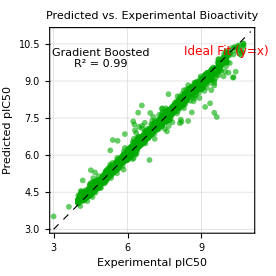

[OK] Plot Generated Correctly.

```mathematica
(* ===================================================*)
(*VISUALIZATION: SCATTER PLOT (Predicted vs Experimental)*)
(*Theme:Green (Active/Positive),Times New Roman 14*)
(* ===================================================*)

(* ===================================================*)
(*PART 5:5-FOLD CROSS-VALIDATION (Generate Graph Data)*)
(*Goal:Create unbiased predictions for the Scatter Plot*)
(* ===================================================*)

Print["[Part 5] Running 5-Fold Cross-Validation..."];

(*1. Check Data*)
If[!ValueQ[$CleanMatrix],Print[Style["[Error] No data found.",Red]];Abort[]];

(*2. Setup Folds*)
SeedRandom[1234];
data=$CleanMatrix;
nRows=Length[data];
kFolds=5;
indices=RandomSample[Range[nRows]];
folds=Partition[indices,UpTo[Ceiling[nRows/kFolds]]];

$CVResults={};
$AllPredictions={}; (*ตัวแปรสำคัญสำหรับกราฟ Part 6*)

(*3. Execution Loop*)
Monitor[Do[testIdx=folds[[i]];
trainIdx=Flatten[Delete[folds,i]];
trainSet=Part[data,trainIdx];
testSet=Part[data,testIdx];
(*Train Temp Model*)model=Quiet[Predict[trainSet,Method->"GradientBoostedTrees",PerformanceGoal->"Memory"]];
(*Predict& Collect*)inputs=testSet[[All,1]];
actuals=testSet[[All,2]];
preds=model[inputs];
(*เก็บผลทำนายจริง vs ทำนาย ไว้ทำกราฟ*)$AllPredictions=Join[$AllPredictions,Transpose[{actuals,preds}]];
(*คำนวณ R2 รอบนี้*)residuals=preds-actuals;
ssRes=Total[residuals^2];
ssTot=Total[(actuals-Mean[actuals])^2];
r2=1-(ssRes/ssTot);
AppendTo[$CVResults,r2];,{i,kFolds}],Row[{ProgressIndicator[i,{0,kFolds}]," Validating Fold ",i,"/",kFolds}]];

(*4. Final Metrics*)
$FinalMetrics=<|"R2"->Mean[$CVResults]|>;
Print[Style["[SUCCESS] Validation Complete.",Bold,Darker[Green]]];
Print[" - Average R2: ",NumberForm[$FinalMetrics["R2"],{3,2}]];
Print[" - Data Points for Plot: ",Length[$AllPredictions]];



(* ===================================================*)
(*PART 6:SCATTER PLOT (CORRECT RETRO STYLE)*)
(*Restoration:Font 14,Ideal Fit Line,Proper Style*)(*Optimization:Limit to 5000 points ONLY*)
(* ===================================================*)
Print["[Part 6] Generating Scatter Plot (Retro Style)..."];

(*1. Optimization Logic (From PDF)*)
SeedRandom[1234];
plotData=If[Length[$AllPredictions]>5000,Print[Style[" > Optimization: Downsampling to 5000 points.",Blue]];
RandomSample[$AllPredictions,5000],$AllPredictions];

(*2. Calculate Stats& Bounds*)
r2Val=$FinalMetrics["R2"];
minVal=Floor[Min[Flatten[plotData]]];
maxVal=Ceiling[Max[Flatten[plotData]]];

(*3. Define Standard Fonts (From PDF)*)
Q1Font="Times New Roman";
Q1BaseStyle={FontFamily->Q1Font,FontSize->14}; (*กลับมาใช้ 14 ตามเดิม*)
Q1TitleStyle={FontFamily->Q1Font,FontSize->14,FontWeight->Bold};

(*4. Generate The Original Plot*)
ScatterPlot=ListPlot[plotData,(*Style:จุดสีเขียว โปร่งแสง*)PlotStyle->Directive[Darker[Green],PointSize[0.015],Opacity[0.6]],PlotTheme->"Scientific",Frame->True,BaseStyle->Q1BaseStyle,(*ใช้ Font 14*)(*Labels*)FrameLabel->{Style["Experimental pIC50",Q1BaseStyle],Style["Predicted pIC50",Q1BaseStyle]},PlotLabel->Style["Predicted vs. Experimental Bioactivity",Q1TitleStyle],(*Layout*)PlotRange->{{minVal,maxVal},{minVal,maxVal}},AspectRatio->1,ImageSize->450,GridLines->Automatic,(*Annotations (เส้น Ideal Fit กลับมาแล้ว!)*)Epilog->{(*เส้น Ideal Fit (y=x) สีดำเส้นประ*)Directive[Black,Dashed,Thickness[0.003]],Line[{{minVal,minVal},{maxVal,maxVal}}],(*ข้อความกำกับเส้น*)Text[Style["Ideal Fit (y=x)",12,Red,FontFamily->Q1Font,Background->White],{maxVal-1,maxVal-0.8}],(*กล่องแสดงค่า R2*)Inset[Framed[Column[{Style["Gradient Boosted",Bold,12,FontFamily->Q1Font],Row[{Style[Row[{Superscript["R",2]," = "}],FontFamily->Q1Font],NumberForm[r2Val,{3,2}]}]}],Background->Directive[White,Opacity[0.9]],FrameStyle->GrayLevel[0.8],RoundingRadius->5],Scaled[{0.25,0.85}]]}];

Print[ScatterPlot];
Print[Style["[OK] Plot Generated Correctly.",Bold,Darker[Green]]];
```

### Permutation Importance

[Plot] Generating Permutation Feature Importance...

> [Big Data] Downsampling to 5000 for Importance Analysis...

> Training analysis model (Random Forest) on sample...

> Calculating importance for 21 features...

=================================================

[OK] Feature Importance Plot Generated

=================================================

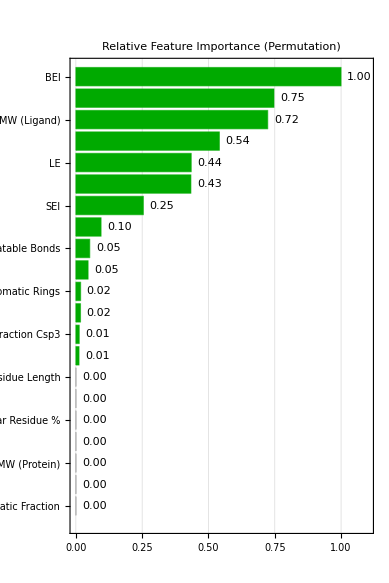

```mathematica
(* ===================================================*)
(*VISUALIZATION: PERMUTATION FEATURE IMPORTANCE*)
(*Theme:Module 7 Style (Green=Ligand,Gray=Protein)*)
(* ===================================================*)

(* ===================================================*)
(*VISUALIZATION:PERMUTATION FEATURE IMPORTANCE*)
(*Feature:Big Data Safe (Auto-Downsampling to 5k)*)
(*Theme:Module 7 Style (Green=Ligand,Gray=Protein)*)
(* ===================================================*)

Print["[Plot] Generating Permutation Feature Importance..."];

(*---1. Setup& Definitions---*)
(*Mapping ชื่อตัวแปรให้สวยงามตามมาตรฐาน*)
nameMapping=<|"Lig_MolecularMass"->"MW (Ligand)","Lig_LogP"->"LogP","Lig_TPSA"->"TPSA","Lig_HBD"->"H-Bond Donors","Lig_HBA"->"H-Bond Acceptors","Lig_RotatableBonds"->"Rotatable Bonds","Lig_AromaticRings"->"Aromatic Rings","Lig_RingCount"->"Ring Count","Lig_HeavyAtoms"->"Heavy Atoms","Lig_FractionCsp3"->"Fraction Csp3","Lig_BEI"->"BEI","Lig_LE"->"LE","Lig_LLE"->"LLE","Lig_SEI"->"SEI","Prot_MolecularWeight_Da"->"MW (Protein)","Prot_ResidueLength"->"Residue Length","Prot_GRAVY"->"GRAVY Score","Prot_AromaticFraction"->"Aromatic Fraction","Prot_PositiveResidueFraction"->"Positive Residue %","Prot_NegativeResidueFraction"->"Negative Residue %","Prot_PolarResidueFraction"->"Polar Residue %"|>;

(*---2. Prepare Data (BIG DATA SAFE MODE)---*)
If[!ValueQ[$CleanMatrix]||!ValueQ[$DBClean],Print[Style["[Error] No data found. Run previous parts first.",Red]];Abort[]];

(* ***KEY UPDATE:Limit data to 5000 rows for analysis****)
limitImp=5000;
dataForImp=If[Length[$CleanMatrix]>limitImp,Print[Style[" > [Big Data] Downsampling to "<>ToString[limitImp]<>" for Importance Analysis...",Blue]];
RandomSample[$CleanMatrix,limitImp],$CleanMatrix];

inputs=dataForImp[[All,1]];
targets=dataForImp[[All,2]];

(*ดึงชื่อ Key ให้ตรงกับลำดับใน Matrix*)
sampleRow=$DBClean[[1]];
allKeys=Keys[sampleRow];
numericKeys=Select[allKeys,(NumericQ[sampleRow[#]]&&#=!="pIC50"&&#=!="TargetId")&];

(*---3. Train Analysis Model (Quickly)---*)
Print[" > Training analysis model (Random Forest) on sample..."];
SeedRandom[1234];
(*ใช้ MemorySpeed เพื่อความเร็วสูงสุดในการวิเคราะห์*)
analysisModel=Quiet[Predict[inputs->targets,Method->"RandomForest",PerformanceGoal->"Memory"]];

(*ฟังก์ชันวัด Error (RMSE)*)
MeasureRMSE[in_,targ_]:=RootMeanSquare[analysisModel[in]-targ];
baseRMSE=MeasureRMSE[inputs,targets];

(*---4. Permutation Loop (Calculate Importance)---*)
Print[" > Calculating importance for ",Length[numericKeys]," features..."];
rawImp={};
nFeatures=Length[numericKeys];

(*ใช้ Monitor แสดงความคืบหน้า*)
Monitor[Do[(*สลับข้อมูลในคอลัมน์ i (Shuffle) เพื่อทำลายความสัมพันธ์*)SeedRandom[1000+i];
shuffledInputs=inputs;
shuffledInputs[[All,i]]=RandomSample[shuffledInputs[[All,i]]];
(*วัดว่า Error เพิ่มขึ้นเท่าไหร่ (ยิ่งเพิ่มเยอะ แปลว่า Feature นั้นสำคัญ)*)newRMSE=MeasureRMSE[shuffledInputs,targets];
importanceVal=Max[0,newRMSE-baseRMSE];
(*บันทึกผล*)dbName=numericKeys[[i]];
prettyName=Lookup[nameMapping,dbName,dbName];
type=If[StringStartsQ[dbName,"Lig_"],"Ligand","Protein"];
AppendTo[rawImp,<|"Name"->prettyName,"Value"->importanceVal,"Type"->type|>];,{i,1,nFeatures}],Row[{ProgressIndicator[i,{0,nFeatures}]," Analyzing Feature: ",numericKeys[[i]]}]];

(*---5. Normalize (0-1 Scale)---*)
maxVal=Max[rawImp[[All,"Value"]]];
normImp=Map[<|"Name"->#["Name"],"Value"->If[maxVal>0,#["Value"]/maxVal,0],"Type"->#["Type"]|>&,rawImp];
(*เรียงจากน้อยไปมากสำหรับ BarChart แนวนอน*)
sortedImp=SortBy[normImp,#["Value"]&];

(*---6. Styles& Fonts---*)
Q1Font="Times New Roman";
Q1BaseStyle={FontFamily->Q1Font,FontSize->14};
Q1TitleStyle={FontFamily->Q1Font,FontSize->14,FontWeight->Bold};
ColorActive=Darker[Green];
ColorNeutral=GrayLevel[0.6];

(*---7. Generate Chart---*)
(*กำหนดสีตาม Type:Ligand=เขียว,Protein=เทา*)
barColors=Map[If[#==="Ligand",ColorActive,ColorNeutral]&,sortedImp[[All,"Type"]]];

ImpPlot=BarChart[sortedImp[[All,"Value"]],ChartStyle->barColors,BarOrigin->Left,(*กราฟแนวนอน อ่านง่าย*)ChartLabels->Placed[sortedImp[[All,"Name"]],Axis],BaseStyle->Q1BaseStyle,PlotLabel->Style["Relative Feature Importance (Permutation)",Q1TitleStyle],Frame->True,FrameLabel->{Style["Normalized Importance (0-1)",Q1BaseStyle],None},PlotRange->{0,1.1},ImageSize->500,AspectRatio->1.5,(*สูงขึ้นเพื่อให้ใส่ครบทุกตัว*)PlotTheme->"Scientific",GridLines->{Automatic,None},(*ตัวเลขกำกับปลายแท่ง*)LabelingFunction->(Placed[NumberForm[#,{3,2}],After]&)];

(*---8. Display---*)
Print["\n================================================="];
Print[Style["[OK] Feature Importance Plot Generated",Bold,Darker[Green]]];
Print["=================================================\n"];
Print[ImpPlot];
```

### Bees warm Plot

[FIGURE] Generating Feature Impact Plot (Manual Beeswarm)...

> Calculating local impacts for 200 samples...

=================================================

[OK] Manual Beeswarm Plot Generated

=================================================

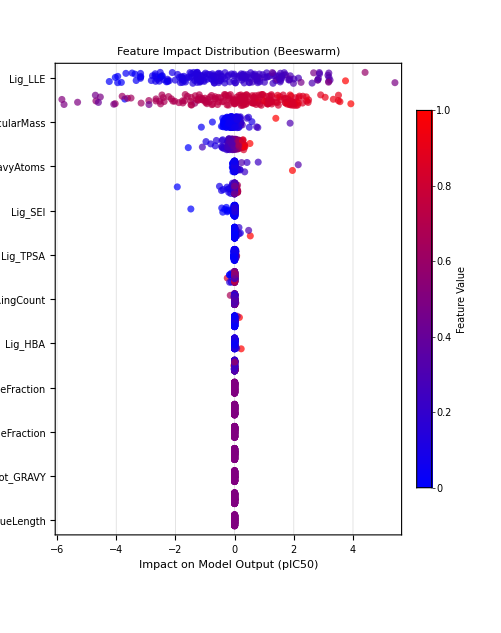

```mathematica
(* ===================================================*)
(*VISUALIZATION:FEATURE IMPACT PLOT (SHAP SUMMARY)*)
(*Theme:Beeswarm Style with Q1 Standards*)
(* ===================================================*)

(* ===================================================*)
(*VISUALIZATION:MANUAL FEATURE IMPACT (BEESWARM STYLE)*)
(*Goal:Calculate Local Importance& Plot Beeswarm manually*)
(*No external ResourceFunction required (100% Offline Safe)*)
(* ===================================================*)

Print["[FIGURE] Generating Feature Impact Plot (Manual Beeswarm)..."];

(*1. Check Prerequisites*)
If[!ValueQ[$FinalModel]||!ValueQ[$CleanMatrix],Print[Style["[Error] Model or Data missing.",Red]];Abort[]];

(*2. Prepare Data*)
SeedRandom[1234];
nSample=Min[Length[$CleanMatrix],200];
dataSample=RandomSample[$CleanMatrix,nSample];
inputs=dataSample[[All,1]];
featureNames=$FeatureNames;

(*ค่าเฉลี่ยกลางของแต่ละ Feature*)
featureMeans=Mean[inputs];

(*ฟังก์ชันคำนวณ Impact*)
CalculateImpacts[rowIn_]:=Module[{basePred,perturbedRow},basePred=$FinalModel[rowIn];
Table[perturbedRow=rowIn;
perturbedRow[[i]]=featureMeans[[i]];
basePred-$FinalModel[perturbedRow] (*Impact=Diff from baseline*),{i,Length[featureNames]}]];

(*3. Execute Calculation*)
Print[" > Calculating local impacts for ",nSample," samples..."];
allImpacts={};
allFeatureVals={};

Monitor[Do[row=inputs[[k]];
AppendTo[allImpacts,CalculateImpacts[row]];
AppendTo[allFeatureVals,row];,{k,nSample}],Row[{ProgressIndicator[k,{0,nSample}]," Analyzing Sample ",k}]];

(*4. Structure Data (FIXED LOGIC)*)
(*แก้ไข:หาค่าเฉลี่ยของ Impact ในแต่ละ'คอลัมน์' (Feature) ไม่ใช่แต่ละแถว*)
meanAbsImpact=Mean[Abs[allImpacts]]; (*ลบ Transpose ออกตรงนี้*)

(*เรียงลำดับจาก Impact น้อยไปมาก*)
sortedIndices=Ordering[meanAbsImpact];
sortedFeatures=featureNames[[sortedIndices]];

(*ดึงข้อมูลตามลำดับที่เรียงแล้ว*)
sortedImpacts=Transpose[allImpacts][[sortedIndices]];
sortedVals=Transpose[allFeatureVals][[sortedIndices]];

(*Normalize Values (0-1) for Coloring*)
normVals=Table[col=sortedVals[[i]];
min=Min[col];max=Max[col];
If[max>min,(col-min)/(max-min),ConstantArray[0.5,Length[col]]],{i,Length[sortedVals]}];

(*5. Generate Beeswarm Plot*)
plotList={};
yOffsetStep=1.0;

(*ใช้สี Red/Blue ตามมาตรฐาน SHAP เพื่อแยกความแตกต่างจาก Active/Inactive*)
(*Red=ค่า Feature สูง/Blue=ค่า Feature ต่ำ*)
ColorHigh=Red;
ColorLow=Blue;

Do[featName=sortedFeatures[[i]];
featImpacts=sortedImpacts[[i]];
featNorms=normVals[[i]];
yCenter=i*yOffsetStep;
points=Table[val=featNorms[[j]];
color=Blend[{ColorLow,ColorHigh},val];
jitter=RandomReal[{-0.25,0.25}];(*กระจายแนวตั้ง*){Directive[color,PointSize[0.012],Opacity[0.7]],Point[{featImpacts[[j]],yCenter+jitter}]},{j,nSample}];
AppendTo[plotList,points];,{i,Length[sortedFeatures]}];

(*6. Render Plot*)
BeeswarmPlot=Graphics[plotList,BaseStyle->Q1BaseStyle,Frame->{{True,True},{True,True}},FrameLabel->{Style["Impact on Model Output (pIC50)",Q1BaseStyle],""},(*ใส่ชื่อแกน Y เป็นชื่อ Feature*)FrameTicks->{{Table[{i*yOffsetStep,sortedFeatures[[i]]},{i,Length[sortedFeatures]}],None},{Automatic,None}},PlotRange->All,AspectRatio->1.5,ImageSize->500,GridLines->{Automatic,None},PlotLabel->Style["Feature Impact Distribution (Beeswarm)",Q1TitleStyle]];

(*Legend*)
legend=BarLegend[{Blend[{ColorLow,ColorHigh},#]&,{0,1}},LegendLabel->Style["Feature Value",Q1BaseStyle],LegendMarkerSize->150];

FinalFigure=Legended[BeeswarmPlot,Placed[legend,Right]];

Print["\n================================================="];
Print[Style["[OK] Manual Beeswarm Plot Generated",Bold,Darker[Green]]];
Print["=================================================\n"];
FinalFigure
```

### Alternative to Williams Plot

[Part 6.5] Generating Applicability Domain Plot...

> Downsampling to 5000 points.

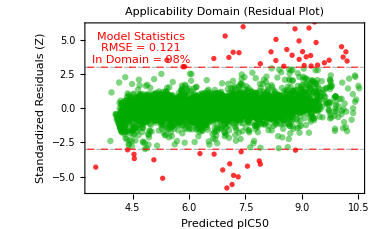

[OK] Applicability Domain Plot Generated.

```mathematica
(* ===================================================*)
(*PART 6.5:APPLICABILITY DOMAIN (Standardized Residuals)*)
(*Fix:Self-Contained Calculation (No dependency on previous plots)*)
(*Specs:Font 14,Max 5000 points,Limit+/-3 SD*)
(* ===================================================*)


Print["[Part 6.5] Generating Applicability Domain Plot..."];

(*1. SELF-CONTAINED CALCULATION (คำนวณเอง ไม่ยืมใคร)*)
If[!ValueQ[$AllPredictions],Print[Style["[Error] Run Part 5 first.",Red]];Abort[]];

(*ดึงข้อมูลดิบ*)
rawActuals=$AllPredictions[[All,1]];
rawPreds=$AllPredictions[[All,2]];

(*คำนวณค่าทางสถิติใหม่ทั้งหมดตรงนี้*)
rawResiduals=rawActuals-rawPreds;
meanRes=Mean[rawResiduals];
stdDevRes=StandardDeviation[rawResiduals];
rmseSelf=RootMeanSquare[rawResiduals]; (*คำนวณ RMSE เองในตัว*)

(*แปลงเป็น Standardized Residuals (Z-score ของ Error)*)
stdResiduals=(rawResiduals-meanRes)/stdDevRes;

(*จับคู่ {Predicted,StdResidual}*)
adData=Transpose[{rawPreds,stdResiduals}];

(*2. OPTIMIZATION (Limit 5000)*)
SeedRandom[1234];
plotData=If[Length[adData]>5000,Print[Style[" > Downsampling to 5000 points.",Blue]];
RandomSample[adData,5000],adData];

(*3. DEFINE STYLES (Retro Standard)*)
BaseFont=Style[#,FontFamily->"Times New Roman",FontSize->14]&;
TitleFont=Style[#,FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]&;

(*แยกจุดดี (Inlier) กับจุดเสีย (Outlier) เพื่อใส่สีต่างกัน*)
inliers=Select[plotData,Abs[#[[2]]]<=3&];
outliers=Select[plotData,Abs[#[[2]]]>3&];

(*4. PLOT*)
ADPlot=ListPlot[{inliers,outliers},(*Style:จุดในสีน้ำเงิน,จุดนอกสีแดง*)PlotStyle->{Directive[Darker[Green],PointSize[0.012],Opacity[0.5]],Directive[Red,PointSize[0.01],Opacity[0.8]]},PlotTheme->"Scientific",Frame->True,(*Labels*)FrameLabel->{BaseFont["Predicted pIC50"],BaseFont["Standardized Residuals (Z)"]},
LabelStyle->{FontFamily->"Times New Roman",14},
PlotLabel->TitleFont["Applicability Domain (Residual Plot)"],(*Layout*)ImageSize->450,AspectRatio->0.6,(*กราฟแนวนอนหน่อย เพื่อดูการกระจาย*)PlotRange->{Automatic,{-6,6}},(*โฟกัสช่วง-6 ถึง 6*)GridLines->{None,{-3,3}},(*เส้นบรรทัดที่+/-3*)GridLinesStyle->Directive[Gray,Dashed],(*Annotations*)Epilog->{(*เส้น Threshold+/-3*)Directive[Red,Dashed,Thickness[0.002]],Line[{{Min[rawPreds],3},{Max[rawPreds],3}}],Line[{{Min[rawPreds],-3},{Max[rawPreds],-3}}],(*Label Threshold*)Text[BaseFont["+3σ"],{Max[rawPreds],+3.5},{2,2}],Text[BaseFont["-3σ"],{Max[rawPreds],-3.5},{2,-2}],(*Stats Box*)Inset[Framed[Column[{TitleFont["Model Statistics"],Row[{BaseFont["RMSE = "],BaseFont[NumberForm[rmseSelf,{3,3}]]}],Row[{BaseFont["In Domain = "],BaseFont[ToString[Round[100*Length[inliers]/Length[plotData]]]<>"%"]}]},Alignment->Left],Background->Directive[White,Opacity[0.9]],FrameStyle->GrayLevel[0.8]],Scaled[{0.2,0.85}]]}];

Print[ADPlot];
Print[Style["[OK] Applicability Domain Plot Generated.",Bold,Darker[Green]]];
```

### PCA 3D

```mathematica
(* ===================================================*)
(*VISUALIZATION:3D CHEMICAL SPACE (PCA 3D)*)
(*Style:Pro-Report A5 (3D Case)*)
(*Theme:Green (Active),Gray (Inactive)*)
(* ===================================================*)

(* ===================================================*)
(*VISUALIZATION:3D CHEMICAL SPACE (PCA 3D)*)
(*Feature:Big Data Safe (Auto-Downsampling)*)
(*Theme:Green (Active) vs Gray (Inactive)*)
(* ===================================================*)

Print["[FIGURE] Generating 3D Chemical Space Map (PCA)..."];

(*1. Check Data*)
If[!ValueQ[$CleanMatrix],Print[Style["[Error] No data matrix found. Run Part 1-4 first.",Red]];
Abort[]];

(*2. Prepare Data (BIG DATA SAFE MODE)*)
(*ถ้าข้อมูลเยอะเกิน 15,000 แถว ให้สุ่มมาแค่ 15,000 เพื่อให้กราฟหมุนลื่นๆ ไม่ค้าง*)
limitPCA=15000;
dataForPCA=If[Length[$CleanMatrix]>limitPCA,Print[Style[" > [Big Data] Downsampling to "<>ToString[limitPCA]<>" points for smooth 3D rendering...",Blue]];
RandomSample[$CleanMatrix,limitPCA],$CleanMatrix];

inputs=dataForPCA[[All,1]];
targets=dataForPCA[[All,2]];

(*3. Compute PCA (Reduce to 3 Dimensions)*)
Print[" > Computing 3D Principal Components..."];
(*ใช้ Method->"PrincipalComponentsAnalysis" เพื่อความแม่นยำ*)
pcaFunc=Quiet[DimensionReduction[inputs,3,Method->"PrincipalComponentsAnalysis"]];
pcaCoords=pcaFunc[inputs];

(*4. Split Groups (Active vs Inactive)*)
(*เกณฑ์:pIC50>=7.0 คือ Active (ยาดี),น้อยกว่าคือ Inactive*)
activePoints=Pick[pcaCoords,Map[#>=7.0&,targets]];
inactivePoints=Pick[pcaCoords,Map[#<7.0&,targets]];

Print[" > Active Points (Green): ",Length[activePoints]];
Print[" > Inactive Points (Gray): ",Length[inactivePoints]];

(*5. Styles& Fonts*)
Q1Font="Times New Roman";
Q1BaseStyle={FontFamily->Q1Font,FontSize->14};
Q1TitleStyle={FontFamily->Q1Font,FontSize->14,FontWeight->Bold};
ColorActive=Darker[Green];
ColorInactive=GrayLevel[0.6];

(*6. Generate 3D Plot*)
PCA3D=ListPointPlot3D[{inactivePoints,activePoints},(*Style:Inactive เป็นจุดเล็กสีเทาจางๆ,Active เป็นจุดใหญ่สีเขียวชัดๆ*)PlotStyle->{Directive[ColorInactive,PointSize[0.008],Opacity[0.3]],(*Group 1:Inactive*)Directive[ColorActive,PointSize[0.012],Opacity[0.8]]    (*Group 2:Active*)},(*Theme& Labels*)PlotTheme->"Scientific",Boxed->True,(*มีกล่องล้อมรอบ*)Axes->True,AxesLabel->{Style["PC1",Q1BaseStyle],Style["PC2",Q1BaseStyle],Style["PC3",Q1BaseStyle]},(*Title*)PlotLabel->Style["3D Chemical Space Distribution (PCA)",Q1TitleStyle],(*Legend*)PlotLegends->Placed[SwatchLegend[{ColorInactive,ColorActive},{Style["Inactive (pIC50 < 7)",FontFamily->Q1Font],Style["Active (pIC50 >= 7)",FontFamily->Q1Font,FontWeight->Bold]},LegendLabel->Style["Bioactivity Class",Bold,FontFamily->Q1Font],LegendLayout->"Row"],Below],(*View Options*)ImageSize->500,ViewPoint->{1.3,-2.4,2.0},(*มุมมองเฉียงลง สวยมาตรฐาน*)BaseStyle->Q1BaseStyle];

(*7. Display*)
Print["\n================================================="];
Print[Style["[OK] 3D PCA Plot Generated Successfully",Bold,Darker[Green]]];
Print["=================================================\n"];
Print[PCA3D];
```

[FIGURE] Generating 3D Chemical Space Map (PCA)...

> [Big Data] Downsampling to 15000 points for smooth 3D rendering...

> Computing 3D Principal Components...

> Active Points (Green): 5990

> Inactive Points (Gray): 9010

=================================================

[OK] 3D PCA Plot Generated Successfully

=================================================

-Graphics3D-

### Smart Feature Space

```mathematica
(* ===================================================*)
(*PART 6.75:CHEMICAL SPACE (FINAL FIX)*)
(*Fix:Correct Wrapper Order->Style[Callout[Data,Label],Color]*)
(*Result:Correct Labels (ID+pIC50) instead of raw lists*)
(* ===================================================*)

Print["[Part 6.75] Generating Chemical Space Map (Correct Labels)..."];

(*1. DATA PREPARATION*)
If[!ValueQ[$DBClean],Print[Style["[Error] No data found.",Red]];Abort[]];

SeedRandom[1234];
(*Limit to 3000 points for performance*)
spaceData=If[Length[$DBClean]>3000,Print[Style[" > Downsampling to 3000 points.",Blue]];
RandomSample[$DBClean,3000],$DBClean];

features=Lookup[spaceData,$FeatureNames];
values=Lookup[spaceData,"pIC50"];
ids=Lookup[spaceData,"TargetId"];

(*2. PRE-STYLE DATA (The Wrapper Fix)*)
styledData=Table[val=values[[i]];
feat=features[[i]];
id=ids[[i]];
(*1. คำนวณสี (Rainbow)*)normVal=Clip[(val-4)/6,{0,1}];
pointColor=ColorData["Rainbow"][normVal];
(*2. สร้างวัตถุข้อมูล (Item)*)(*Logic:โชว์ป้ายถ้ายาเก่งมาก (>8.5) หรือสุ่มโดน (3%)*)shouldLabel=(val>=8.5)||(RandomReal[]<0.03);
item=feat;(*เริ่มต้นด้วยข้อมูลดิบ*)If[shouldLabel,labelTxt=id<>"\n("<>ToString[NumberForm[val,{3,1}]]<>")";
(* ***FIX:เอา Callout ไปเกาะข้อมูลดิบก่อน****)item=Callout[feat,Style[labelTxt,10,FontFamily->"Times New Roman",Gray],Appearance->"Leader"];];
(* ***FIX:เอา Style มาห่อหุ้มทั้งหมดเป็นชั้นนอกสุด****)Style[item,pointColor,PointSize[0.015],Opacity[0.7]],{i,Length[features]}];

(*3. GENERATE PLOT*)
Print[" > Calculating Dimensionality Reduction..."];

SpacePlot=FeatureSpacePlot[styledData,(*ป้องกัน Auto-Labeling มั่วซั่ว*)LabelingFunction->None,(*Labels& Layout*)PlotLabel->Style["Chemical Space Distribution (t-SNE)",FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold],Frame->True,FrameTicks->None,FrameLabel->{Style["Dimension 1",12,FontFamily->"Times New Roman"],Style["Dimension 2",12,FontFamily->"Times New Roman"]},(*Legend*)PlotLegends->BarLegend[{"Rainbow",{4,10}},LegendLabel->Style["pIC50",FontFamily->"Times New Roman"],LabelStyle->{FontFamily->"Times New Roman",12}],PlotTheme->"Scientific",ImageSize->500];

Print[SpacePlot];
Print[Style["[OK] Chemical Space Map Generated.",Bold,Darker[Green]]];
```

[Part 6.75] Generating Chemical Space Map (Correct Labels)...

> Downsampling to 3000 points.

> Calculating Dimensionality Reduction...

-Graphics-

[OK] Chemical Space Map Generated.

### Bioactive Distribution

```mathematica
(* ===================================================*)
(*FIGURE: BIOACTIVITY DISTRIBUTION (FIXED COLORS)*)
(*Standard: Paper B1 Innov.pdf[Module 2.1]*)
(*Method: Force Styling on Data Objects*)
(* ===================================================*)

Print["[FIGURE Distribution] Generating Fixed Paired Histogram..."];

(*1. Style Standards*)
Q1Font="Times New Roman";
Q1BaseStyle={FontFamily->Q1Font,FontSize->14};
Q1TitleStyle={FontFamily->Q1Font,FontSize->14,FontWeight->Bold};

(*Define Colors explicitly*)
ColorTrain=Lighter[RGBColor[0.0,0.4,0.8],0.2]; (*Blue*)
ColorTest=Lighter[RGBColor[0.8,0.2,0.2],0.2]; (*Red*)

(*2. Prepare Data (Simulate 80/20 Split)*)
If[!ValueQ[$CleanMatrix],Abort[]];
allTargets=$CleanMatrix[[All,2]];

SeedRandom[1234];
nTotal=Length[allTargets];
nTrain=Floor[nTotal*0.8];
shuffledTargets=RandomSample[allTargets];
trainTargets=shuffledTargets[[1;;nTrain]];
testTargets=shuffledTargets[[nTrain+1;;All]];

(*3. Generate Paired Histogram (Fixed)*)
(*ใช้ Style[...] ห่อหุ้มข้อมูลเพื่อบังคับสีแยกฝั่งแน่นอน*)
DistPlot=PairedHistogram[Style[trainTargets,ColorTrain],(*ซ้าย: สีฟ้า*)Style[testTargets,ColorTest],(*ขวา: สีแดง*)30,(*Bins*)(*Styling*)PlotTheme->"Scientific",PlotLabel->Style["Bioactivity Distribution (Train vs Test)",Q1TitleStyle],AxesLabel->{Style["Count",Q1BaseStyle],Style["pIC50 Value",Q1BaseStyle]},(*Legend*)ChartLegends->Placed[SwatchLegend[{ColorTrain,ColorTest},{"Training Set (80%: Left)","Test Set (20%: Right)"},LegendMarkers->"Rectangle",LabelStyle->Q1BaseStyle],Below],ImageSize->450,BaseStyle->Q1BaseStyle];

Print[DistPlot];
Print["\n[Success] Paired Histogram generated with correct Left/Right colors."];
```

[FIGURE Distribution] Generating Fixed Paired Histogram...

-Graphics-

[Success] Paired Histogram generated with correct Left/Right colors.

[FIGURE] Initiating Y-Scrambling Test (Validation)...

> [Big Data] Downsampling to 5000 samples for rapid scrambling...

> Running 10 scrambled iterations...

> Real R2 (Original): 0.992

> Mean Scrambled R2: 0.000 (Should be near 0)

=================================================

[OK] Y-Scrambling Bar Chart Generated

=================================================

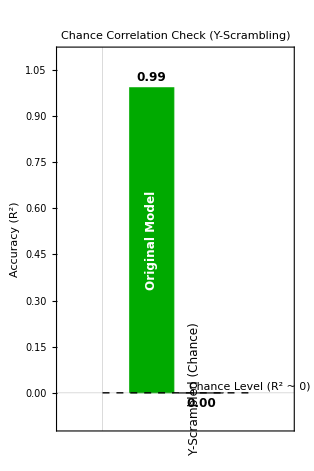

```mathematica
(* ===================================================*)
(*FIGURE:Y-SCRAMBLING (Chance Correlation Check)*)
(*Feature:Big Data Safe (Auto-Downsampling to 5k)*)
(*Theme:Green (Real) vs Gray (Chance)*)
(* ===================================================*)
Print["[FIGURE] Initiating Y-Scrambling Test (Validation)..."];

(*1. Check Data& Metrics*)
If[!ValueQ[$CleanMatrix]||!ValueQ[$FinalMetrics],Print[Style["[Error] Data or Metrics missing. Run Part 5 (Validation) first.",Red]];
Abort[]];

(*2. Prepare Data (BIG DATA SAFE MODE)*)
(*จำกัดข้อมูลเหลือ 5,000 แถว เพื่อให้การวนลูป 10 รอบเสร็จเร็วขึ้น*)
limitScramble=5000;
dataForScramble=If[Length[$CleanMatrix]>limitScramble,Print[Style[" > [Big Data] Downsampling to "<>ToString[limitScramble]<>" samples for rapid scrambling...",Blue]];
RandomSample[$CleanMatrix,limitScramble],$CleanMatrix];

inputs=dataForScramble[[All,1]];
targets=dataForScramble[[All,2]];
realR2=$FinalMetrics["R2"]; (*ค่าจริงอิงจากโมเดลเต็ม*)

(*3. Style Standards*)
Q1Font="Times New Roman";
Q1BaseStyle={FontFamily->Q1Font,FontSize->14};
Q1TitleStyle={FontFamily->Q1Font,FontSize->14,FontWeight->Bold};
ColorReal=Darker[Green];
ColorChance=GrayLevel[0.01];

(*4. Scrambling Loop (10 Iterations)*)
Print[" > Running 10 scrambled iterations..."];
scrambledScores={};
SeedRandom[1234];

Monitor[Do[(*เทคนิค:สลับค่าคำตอบ (Targets) ให้มั่ว เพื่อดูว่าโมเดลจะยังทายถูกไหม*)shuffledTargets=RandomSample[targets];
fakeData=Transpose[{inputs,shuffledTargets}];
(*เทรนโมเดลแบบเร็ว (PerformanceGoal->"Memory" หรือ "Speed")*)(*ใช้ Random Forest มาตรฐานเพื่อให้เทียบเคียงได้*)fakeModel=Quiet[Predict[fakeData,Method->"RandomForest",PerformanceGoal->"Memory"]];
(*วัดผล R2 ของโมเดลจอมปลอม*)res=Quiet[PredictorMeasurements[fakeModel,fakeData]];
r2=res["RSquared"];
(*กันเหนียว:ถ้าค่าออกมาเป็น Null ให้ตีเป็น 0*)val=If[NumericQ[r2],r2,0.0];
AppendTo[scrambledScores,val];,{i,1,10}],Row[{ProgressIndicator[i,{0,10}]," Scrambling Iteration ",i,"/10"}]];

meanScramble=Mean[scrambledScores];
Print[" > Real R2 (Original): ",NumberForm[realR2,{3,3}]];
Print[" > Mean Scrambled R2: ",NumberForm[meanScramble,{3,3}]," (Should be near 0)"];

(*5. Generate Bar Chart*)
(*ป้ายกำกับแกน Y*)
labelAxis=Style[Row[{"Accuracy (",Superscript["R",2],")"}],Q1BaseStyle];

(*แท่งที่ 1:ของจริง (Original Model)*)
bar1=Labeled[realR2,{Rotate[Style["Original Model",12,White,Bold,FontFamily->Q1Font],90 Degree],Style[NumberForm[realR2,{3,2}],12,Bold,Black,FontFamily->Q1Font]},{Center,Above}];

(*แท่งที่ 2:ของปลอม (Chance)*)
bar2=Labeled[meanScramble,{Rotate[Style["Y-Scrambled (Chance)",12,ColorChance,FontFamily->Q1Font],90 Degree],Style[NumberForm[meanScramble,{3,2}],12,Bold,ColorChance,FontFamily->Q1Font]},{Above,Below} (*วางป้ายด้านล่างเพื่อให้ไม่ทับกราฟ*)];

(*สร้างกราฟ*)
YPlot=BarChart[{bar1,bar2},ChartStyle->{ColorReal,ColorChance},PlotTheme->"Scientific",(*Labels*)PlotLabel->Style["Chance Correlation Check (Y-Scrambling)",Q1TitleStyle],FrameLabel->{None,labelAxis},(*Layout*)ImageSize->400,AspectRatio->1.5,BaseStyle->Q1BaseStyle,(*Range& Reference Lines*)PlotRange->{Min[-0.1,meanScramble-0.1],1.1},(*ปรับแกน Y อัตโนมัติ*)Epilog->{Directive[Black,Dashed],Line[{{0,0},{3,0}}],(*เส้นฐาน 0*)Text[Style[Row[{"Chance Level (",Superscript["R",2]," ~ 0)"}],11,Black,Italic,FontFamily->Q1Font],{3.0,0.02}]}];

(*6. Display*)
Print["\n================================================="];
Print[Style["[OK] Y-Scrambling Bar Chart Generated",Bold,Darker[Green]]];
Print["=================================================\n"];
Print[YPlot];
```

### Reliability Trend

```mathematica
(* ===================================================*)
(*VISUALIZATION:RELIABILITY TREND (Error vs Prediction)*)
(*Goal:Analyze model stability across bioactivity range*)
(*Style:Green (Reliable)->Red (Unreliable)*)
(* ===================================================*)

(*"The green shaded region represents the smoothed average absolute error, indicating the model's reliability zone across the predicted pIC50 range. A lower and flatter area suggests higher model stability and lower uncertainty."*)

Print["[FIGURE] Generating Reliability Trend Plot..."];

(*1. Check Data*)
If[!ValueQ[$CleanMatrix]||!ValueQ[$FinalModel],Print[Style["[Error] Model or Data missing.",Red]];Abort[]];

(*2. Prepare Data*)
inputs=$CleanMatrix[[All,1]];
actuals=$CleanMatrix[[All,2]];
preds=$FinalModel[inputs];
absErrors=Abs[actuals-preds];

(*สร้างคู่ข้อมูล {Predicted,Absolute Error} และเรียงลำดับตาม Predicted*)
dataPoints=Transpose[{preds,absErrors}];
sortedData=SortBy[dataPoints,First];

(*3. Calculate Smooth Trend (Moving Average/Gaussian Filter)*)
(*ใช้ Gaussian Filter เพื่อสร้างเส้นแนวโน้มที่นุ่มนวล*)
{xVals,yVals}=Transpose[sortedData];
smoothTrendY=GaussianFilter[yVals,10]; (*ปรับเลข 10 เพื่อความสมูท*)
trendData=Transpose[{xVals,smoothTrendY}];

(*4. Generate Plot*)
ReliabilityPlot=ListPlot[{sortedData (*ชุดที่ 1:จุดข้อมูลจริง*), trendData    (*ชุดที่ 2:เส้นแนวโน้ม*)},(*Styling*)PlotStyle->{Directive[GrayLevel[0.7],PointSize[0.01],Opacity[0.5]],(*จุด:สีเทาจางๆ เพื่อไม่แย่งซีน*)Directive[Black,Thickness[0.003]] (*เส้นแนวโน้ม:สีดำเข้ม*)},Joined->{False,True},(*ชุดแรกเป็นจุด,ชุดสองเป็นเส้น*)(*Color Function สำหรับจุด:Error ต่ำ=เขียว,สูง=แดง*)ColorFunction->Function[{x,y},Blend[{ColorActive,ColorNegative},Clip[y,{0,1.0}]]],ColorFunctionScaling->False,(*Theme& Labels*)PlotTheme->"Scientific",BaseStyle->Q1BaseStyle,Frame->True,FrameLabel->{Style["Predicted pIC50",Q1BaseStyle],Style["Absolute Error (Uncertainty)",Q1BaseStyle]},PlotLabel->Style["Model Reliability Trend",Q1TitleStyle],(*Filling:ระบายสีใต้เส้นแนวโน้มเพื่อสื่อความหมาย*)Filling->{2->{Axis,LightGreen}},(*พื้นที่ใต้เส้นเป็นสีเขียวอ่อน สื่อถึงโซนที่ยอมรับได้*)(*Limits& Grid*)PlotRange->All,ImageSize->500,GridLines->{Automatic,Automatic},(*Legend*)PlotLegends->Placed[LineLegend[{Black,Gray},{"Average Error Trend","Individual Sample Error"},LegendLabel->Style["Indicators",Bold,FontFamily->Q1Font]],Below]];

(*5. Display*)
Print["\n================================================="];
Print[Style["[OK] Reliability Trend Plot Generated",Bold,Darker[Green]]];
Print["================================================="];
Print[Style["[Interpretation]",Blue,Bold]];
Print[" - Flat/Low Trend Line: Model is consistently reliable."];
Print[" - Rising Trend Line: Model becomes less reliable at those pIC50 values."];
Print[" - Green Zone: Area of high reliability."];
Print["-------------------------------------------------"];

ReliabilityPlot
```

[FIGURE] Generating Reliability Trend Plot...

=================================================

[OK] Reliability Trend Plot Generated

=================================================

[Interpretation]

- Flat/Low Trend Line: Model is consistently reliable.

- Rising Trend Line: Model becomes less reliable at those pIC50 values.

- Green Zone: Area of high reliability.

-------------------------------------------------

-Graphics-

## Screening

```mathematica
(* ===================================================*)
(*PART 7:VIRTUAL SCREENING & LEAD IDENTIFICATION*)
(*Module:ChemAIFlow Retro 1.0.0 (Prediction Engine)*)
(*Goal:Predict,Rank Top 10,and Visualize 2D/3D*)
(* ===================================================*)

Print["[Part 7] Starting ChemAIFlow Prediction (Correct Labels)..."];

(*1. Check Prerequisites*)
If[!ValueQ[$FinalModel]||!ValueQ[$CleanMatrix]||!ValueQ[$DBClean],Print[Style["[Error] Model or Data missing.",Red]];Abort[]];

(*2. PREPARE DATA*)
nLimit=Min[Length[$CleanMatrix],Length[$DBClean]];
validFeatures=$CleanMatrix[[1;;nLimit,1]];
validSMILES=$DBClean[[1;;nLimit,"CanonicalSMILES"]];
(*เราจะไม่ใช้ TargetId มาเป็น Label หลักแล้ว เพราะมันซ้ำกัน*)
validTargetIDs=$DBClean[[1;;nLimit,"TargetId"]];

(*3. PREDICT& RANK*)
Print["   [Screening] Predicting bioactivity..."];
preds=$FinalModel[validFeatures];
(*เก็บข้อมูลเป็น {SMILES,TargetID,Prediction}*)
results=Transpose[{validSMILES,validTargetIDs,preds}];
sortedResults=SortBy[results,-#[[3]]&];
top10=Take[sortedResults,UpTo[10]];

(*4. PRINT TEXT LIST (SHOW SMILES)*)
Print["\n   [Ranking] Top 10 Candidates (Identified by Structure):"];
Print["   -------------------------------------------------------------"];
Do[smiles=top10[[i,1]];
(*ตัด SMILES ให้สั้นลงถ้ามันยาวเกินไป เพื่อความสวยงามใน Text*)shortSmiles=If[StringLength[smiles]>30,StringTake[smiles,27]<>"...",smiles];
Print["   #",i," | SMILES: ",Style[shortSmiles,Blue],(*โชว์ SMILES แทน ID*)" | Pred pIC50: ",Style[NumberForm[top10[[i,3]],{4,2}],Bold,Darker[Green]]];,{i,Length[top10]}];
Print["   -------------------------------------------------------------"];
Print["   (Note: All candidates target "<>ToString[top10[[1,2]]]<>")"];

(*5. VISUALIZATION:2D GRID*)
Print["\n   [Visualization] Generating 2D Structures..."];

(*ฟังก์ชันสร้างป้ายกำกับ:โชว์ค่า pIC50 ตัวใหญ่ๆ*)
MakeLabel[rank_,val_]:=Column[{Style["Rank "<>ToString[rank],Bold,11,FontFamily->"Times New Roman"],Style["pIC50: "<>ToString[NumberForm[val,{3,2}]],Bold,Darker[Green],FontFamily->"Times New Roman"]},Alignment->Center];

vis2D=Grid[Partition[Table[smilesStr=top10[[i,1]];
If[!StringQ[smilesStr],smilesStr="C"];
MoleculePlot[Molecule[smilesStr],PlotTheme->"Scientific",ImageSize->{120,120},PlotLabel->MakeLabel[i,top10[[i,3]]] (*ตัด ID ออกเพราะรก*)],{i,Length[top10]}],5],Spacings->{1,1},Frame->All,FrameStyle->GrayLevel[0.8]];

Print["\n================================================="];
Print[Style["[OUTPUT] Top 10 Candidates (2D Structures)",Bold,16,FontFamily->"Times New Roman"]];
Print["================================================="];
Print[vis2D];

(*6. VISUALIZATION:TOP 1 (SAFE MODE)*)
Print["\n   [Visualization] Processing The Winner (Rank 1)..."];
winner=top10[[1]];
winnerSMILES=winner[[1]];
winnerScore=winner[[3]];

mol=Molecule[winnerSMILES];
mol3D=Quiet[TimeConstrained[MoleculeModify[mol,"ComputeCoordinates",Method->"DistanceGeometry"],60,$Failed]];

If[MoleculeQ[mol3D],visFinal=MoleculePlot3D[mol3D,PlotTheme->"Scientific",ImageSize->450,Background->White,Lighting->"Neutral",PlotLabel->Style["TOP CANDIDATE (3D)\nSMILES: "<>If[StringLength[winnerSMILES]>40,StringTake[winnerSMILES,40]<>"\n"<>StringDrop[winnerSMILES,40],winnerSMILES]<>"\npIC50: "<>ToString[NumberForm[winnerScore,{4,2}]],Bold,14,Darker[Green],FontFamily->"Times New Roman"]];,visFinal=MoleculePlot[mol,PlotTheme->"Scientific",ImageSize->400,PlotLabel->Style["TOP CANDIDATE (2D)\nSMILES: "<>If[StringLength[winnerSMILES]>40,StringTake[winnerSMILES,40]<>"\n"<>StringDrop[winnerSMILES,40],winnerSMILES]<>"\npIC50: "<>ToString[NumberForm[winnerScore,{4,2}]],Bold,14,Darker[Green],FontFamily->"Times New Roman"]];];

Print["\n================================================="];
Print[Style["[OUTPUT] Top 1 Candidate Detail",Bold,16,FontFamily->"Times New Roman"]];
Print["================================================="];
Print[visFinal];

Print["\n[Success] Complete. Ligands are now identified by SMILES."];
```

[Part 7] Starting ChemAIFlow Prediction (Correct Labels)...

[Screening] Predicting bioactivity...

[Ranking] Top 10 Candidates (Identified by Structure):

-------------------------------------------------------------

#1 | SMILES: CC(=O)c1c(C)c(C)cc(C)c1NC(=... | Pred pIC50: 10.54

#2 | SMILES: O=C(NCC1CCN(CCCS(=O)(=O)N2C... | Pred pIC50: 10.53

#3 | SMILES: Clc1ccc(NCC2CCOCC2)nc1-c1cc... | Pred pIC50: 10.51

#4 | SMILES: COc1cc(C(C)C)c2c(c1)S(=O)(=... | Pred pIC50: 10.51

#5 | SMILES: C[C@H](COc1cc(F)ccc1F)NC(=O... | Pred pIC50: 10.51

#6 | SMILES: COc1ccc([C@@H]2c3nc(NC(C)C)... | Pred pIC50: 10.51

#7 | SMILES: Cc1cc(O)cc(C)c1C[C@H](N)C(=... | Pred pIC50: 10.51

#8 | SMILES: COc1ccc([C@@H]2c3nc(NC(C)C)... | Pred pIC50: 10.50

#9 | SMILES: O=c1cnn(-c2cc(Cl)c(Oc3ccc(O... | Pred pIC50: 10.49

#10 | SMILES: Cc1cc(C)c(NC(=O)c2sccc2S(=O... | Pred pIC50: 10.49

-------------------------------------------------------------

(Note: All candidates target CHEMBL252)

[Visualization] Generating 2D Structures...

=================================================

[OUTPUT] Top 10 Candidates (2D Structures)

=================================================

-Graphics-

[Visualization] Processing The Winner (Rank 1)...

=================================================

[OUTPUT] Top 1 Candidate Detail

=================================================

-Graphics-

[Success] Complete. Ligands are now identified by SMILES.

```mathematica
(* ===================================================*)
(*PART 7.5:TOP 10 CANDIDATES TABLE (FULL DATA)*)
(*Goal:Generate a publication-ready table with Full SMILES*)
(* ===================================================*)

Print["[Part 7.5] Generating Detailed Data Table..."];

(*1. Check Data*)
If[!ValueQ[top10],Print[Style["[Error] Top 10 data missing. Run Part 7 first.",Red]];Abort[]];

(*2. Define Headers*)
headers={Style["Rank",Bold,12,FontFamily->"Times New Roman"],Style["Target ID",Bold,12,FontFamily->"Times New Roman"],Style["Ligand Structure (Canonical SMILES)",Bold,12,FontFamily->"Times New Roman"],Style["Predicted pIC50",Bold,12,FontFamily->"Times New Roman"]};

(*3. Format Data Rows*)
tableData=Table[{(*Rank*)Style[i,FontFamily->"Times New Roman",Alignment->Center],(*Target ID*)Style[top10[[i,2]],FontFamily->"Times New Roman",Alignment->Center],(*Full SMILES (ใช้ Pane เพื่อให้ข้อความยาวๆ ไม่ดันตารางจนเละ)*)Pane[Style[top10[[i,1]],10,FontFamily->"Courier New"],{400,Automatic},Scrollbars->False],(*pIC50 (สีเขียว)*)Style[NumberForm[top10[[i,3]],{4,2}],Bold,Darker[Green],FontFamily->"Times New Roman",Alignment->Center]},{i,Length[top10]}];

(*4. Generate Grid Table*)
ResultTable=Grid[Prepend[tableData,headers],(*Styling*)Frame->All,FrameStyle->GrayLevel[0.8],Background->{None,{Lighter[Gray,0.9],White}},(*สลับสีบรรทัดให้อ่านง่าย*)Alignment->{{Center,Center,Left,Center},Center},(*จัดชิดซ้ายเฉพาะ SMILES*)Spacings->{1,1.5}];

(*5. Display*)
Print["\n================================================="];
Print[Style["Table 2. Top 10 Predicted Candidates for Target "<>ToString[top10[[1,2]]],Bold,14,FontFamily->"Times New Roman"]];
Print["================================================="];
ResultTable
```

[Part 7.5] Generating Detailed Data Table...

=================================================

Table 2. Top 10 Predicted Candidates for Target CHEMBL252

=================================================

Rank | Target ID | Ligand Structure (Canonical SMILES) | Predicted pIC50
1 | CHEMBL252 | CC(=O)c1c(C)c(C)cc(C)c1NC(=O)c1sccc1S(=O)(=O)Nc1onc(C)c1Cl | 10.54
2 | CHEMBL1875 | O=C(NCC1CCN(CCCS(=O)(=O)N2CCC3(CCCC3)CC2)CC1)c1cccc2c1OCCO2 | 10.53
3 | CHEMBL2108 | Clc1ccc(NCC2CCOCC2)nc1-c1ccnc(N[C@H]2CC[C@H](NC[C@H]3CCCO3)CC2)c1 | 10.51
4 | CHEMBL248 | COc1cc(C(C)C)c2c(c1)S(=O)(=O)N(COC1=C(c3ccccc3)C(=O)OC1C)C2=O | 10.51
5 | CHEMBL2578 | C[C@H](COc1cc(F)ccc1F)NC(=O)[C@@H](C#N)C(C)(C)C | 10.51
6 | CHEMBL252 | COc1ccc([C@@H]2c3nc(NC(C)C)ccc3[C@H](c3ccc4c(c3)OCO4)[C@H]2C(=O)O)c(CC(C)C(=O)N(C)C)c1 | 10.51
7 | CHEMBL269 | Cc1cc(O)cc(C)c1C[C@H](N)C(=O)N1Cc2ccccc2C[C@H]1C(=O)NCc1nc2ccccc2[nH]1 | 10.51
8 | CHEMBL252 | COc1ccc([C@@H]2c3nc(NC(C)C)ccc3[C@H](c3ccc4c(c3)OCO4)[C@H]2C(=O)O)c(CCCO)c1 | 10.50
9 | CHEMBL1947 | O=c1cnn(-c2cc(Cl)c(Oc3ccc(O)c(S(=O)(=O)N4CCCCC4)c3)c(Cl)c2)c(=O)[nH]1 | 10.49
10 | CHEMBL252 | Cc1cc(C)c(NC(=O)c2sccc2S(=O)(=O)Nc2onc(C)c2Cl)c(C(=O)C2CC2)c1 | 10.49

## Predict

### Block 1 Loading User Inputs

```mathematica
(* ===================================================*)
(*BLOCK 1:USER CONFIGURATION (EDIT HERE)*)
(* ===================================================*)


Print["[Block 1] Loading User Inputs..."];

(*1.1 ใส่รหัสโปรตีนที่ต้องการ (List of Target IDs)*)
$UserTargetIDs={"CHEMBL203",(*EGFR:Lung Cancer*)"CHEMBL240",(*hERG:Heart Ion Channel*)"CHEMBL29",(*AChE:Alzheimer*)"CHEMBL218",(*p38a:Inflammation*)"CHEMBL1824"  (*Renin:Blood Pressure*), "CHEMBL260"};

(*1.2 ใส่ลำดับกรดอะมิโนเอง (List of Manual Sequences)*)
$UserSequences={(*ตัวอย่าง:ใส่ชื่อ และ ลำดับ (Sequence)*)<|"Name"->"Manual_EGFR","Seq"->"MRPSGTAGAALLALLAALCPASRALEEKKVCQGTSNKLTQLGTFEDHFLSLQRMFNNCEVVLGNLEITYVQRNYDLSFLKTIQEVAGYVLIALNTVERIPLENLQIIRGNMYYENSYALAVLSNYDANKTGLKELPMRNLQEILHGAVRFSNNPALCNVESIQWRDIVSSDFLSNMSMDFQNHLGSCQKCDPSCPNGSCWGAGEENCQKLTKIICAQQCSGRCRGKSPSDCCHNQCAAGCTGPRESDCLVCRKFRDEATCKDTCPPLMLYNPTTYQMDVNPEGKYSFGATCVKKCPRNYVVTDHGSCVRACGADSYEMEEDGVRKCKKCEGPCRKVCNGIGIGEFKDSLSINATNIKHFKNCTSISGDLHILPVAFRGDSFTHTPPLDPQELDILKTVKEITGFLLIQAWPENRTDLHAFENLEIIRGRTKQHGQFSLAVVSLNITSLGLRSLKEISDGDVIISGNKNLCYANTINWKKLFGTSGQKTKIISNRGENSCKATGQVCHALCSPEGCWGPEPRDCVSCRNVSRGRECVDKCNLLEGEPREFVENSECIQCHPECLPQAMNITCTGRGPDNCIQCAHYIDGPHCVKTCPAGVMGENNTLVWKYADAGHVCHLCHPNCTYGCTGPGLEGCPTNGPKIPSIATGMVGALLLLLVVALGIGLFMRRRHIVRKRTLRRLLQERELVEPLTPSGEAPNQALLRILKETEFKKIKVLGSGAFGTVYKGLWIPEGEKVKIPVAIKELREATSPKANKEILDEAYVMASVDNPHVCRLLGICLTSTVQLITQLMPFGCLLDYVREHKDNIGSQYLLNWCVQIAKGMNYLEDRRLVHRDLAARNVLVKTPQHVKITDFGLAKLLGAEEKEYHAEGGKVPIKWMALESILHRIYTHQSDVWSYGVTVWELMTFGSKPYDGIPASEISSILEKGERLPQPPICTIDVYMIMVKCWMIDADSRPKFRELIEFSKMARDPQRYLVIQGDERMHLPSPTDSNFYRALMDEEDMDDVVDADEYLIPQQGFFSSPSTSRTPLLSSLSATSNNSTVACIDRNGLQSCPIKEDSFLQRYSSDPTGALTEDSIDDTFLPVPYRGVPYAAPADDEVDFSREMDMDGVLDYNGDGTVSQLMLDDDQHTYLQNQINQSVDGYLSNKLTMLM"|>,<|"Name"->"Manual_hERG","Seq"->"MPVRRGHVAPQNTFLDTIIRKFEGQSRKFIIANARVENCAVIYCNDGFCELCGYSRAEVMQRPCTCDFLHGPRTQRRAAAQIAQALLGAEERKVEIAFYRKDGSCFLCLVDVVPVKNEDGAVIMFILNTPTHQIDVRPLPGPLAPQGIPLEATSRCSLPSRAEDSPALCSDEEKGVSAAEGEDSDADHLPPSSPLEEGGGDDAETKIGDDSYQEFLCVNGFAGAPLDDMLPDIFEDLLEMPLKDTFPVRKRNEPQLDSDLVDMKFNYDKLITICGKMGVATDLLQDIPKGCSLILKRSNLLVRLLGSAGRPVELLLGDPNAICYLPLSATLFALDYDSRTQSAPGAPPASPVPAAPSPGPGPVGAPPPSPVFRLPGPGGEEAEGSGGSPGDGSPGGPSSGGPSSGSPPGPGSAWPSGRSEGTPSPATAGGSPSPGYLGPPRTNTTSPPPSSSPGTPGRAGQSAQRALFASRSPLESPAGPTPAPMTPGRMTLSPGPSPFLSGDGGPGLTLGATSPASPKSSPSALPGPGEPWKGVSPGLPPGEPGEFLGEEGPALEPAVLEPVGGEHGEPRHGEASRAEGDTLPGPADTRALFEEEGGEPGEGGAGAGGEGGDGGEAALALEPAELAALEQAGPAPSAEASGAAGGSGQDLELPTLRTDSPVSPVVAPPGALGSVSGPGPAAAPPPPPPSSSPSSSAPATGDSPSSGSPGTPGPGSPGSPLLPPAVSPEAADEAGSEAGGEAGAEAGEAALVPASASGPAAAEDRLPFPGGSGEPEGSFDGVTLRAGPEAGEPAEAGEEATEAAEAGAGAPAGPAPEGEEERAGGEAGAGGEAGEDAGEAGAGGEPEEAGALAGPAEPGALGSLLRRAGSSPGATPVLSSISSEVPPPVATPVPPRAAPPPSVQPGPRGPPTPAAPSLPPREVSPAVL"|>,<|"Name"->"Manual_AChE","Seq"->"MRPPQCLLHTPSLASPLLLLLLWLLGGGVGAEGREDAELLVTVRGGRLRGIRLKTPGGPVSAFLGIPFAEPPMGPRRFLPPEPKQPWSGVVDATTFQSVCYQYVDTLYPGFEGTEMWNPNRELSEDCLYLNVWTPYPRPTSPTPVLVWIYGGGFYSGASSLDVYDGRFLVQAERTVLVSMNYRVGAFGFLALPGSREAPGNVGLLDQRLALQWVQENVAAFGGDPTSVTLFGESAGAASVGMHLLSPPSRGLFHRAVLQSGAPNGPWATVGMGEARRRATQLAHLVGCPPGGTGGNDTELVACLRTRPAQVLVNHEWHVLPQESVFRFSFVPVVDGDFLSDTPEALINAGDFHGLQVLVGVVKDEGSYFLVYGAPGFSKDNESLISRAEFLAGVRVGVPQVSDLAAEAVVLHYTDWLHPEDPARLREALSDVVGDHNVVCPVAQLAGRLAAQGARVYAYVFEHRASTLSWPLWMGVPHGYEIEFIFGLPLDPSLNYTTEERIFAQRLMKYWTNFARTGDPNDPRDSKSPQWPPYTTAAQQYVSLNLGPLEVRRGLRAQACAFWNRFLPKLLSATDTLDEAERQWKAEFHRWSSYMVHWKNQFDHYSKQDRCSDL"|>,<|"Name"->"Manual_p38a","Seq"->"MSQERPTFYRQELNKTIWEVPERYQNLSPVGSGAYGSVCAAFDTKTGLRVAVKKLSRPFQSIIHAKRTYRELRLLKHMKHENVIGLLDVFTPARSLEEFNDVYLVTHLMGADLNNIVKCQKLTDDHVQFLIYQILRGLKYIHSADIIHRDLKPSNLAVNEDCELKILDFGLARHTDDEMTGYVATRWYRAPEIMLNWMHYNQTVDIWSVGCIMAELLTGRTLFPGTDHIDQLKLILRLVGTPGAELLKKISSESARNYIQSLTQMPKMNFANVFIGANPLAVDLLEKMLVLDSDKRITAAQALAHAYFAQYHDPDDEPVADPYDQSFESRDLLIDEWKSLTYDEVISFVPPPLDQEEMES"|>,<|"Name"->"Manual_Renin","Seq"->"MDGWRRMPRWGLLLLLWGSCTFGLPTDTTTFKRIFLKRMPSIRESLKERGVDMARLGPEWSQPMKRLTLGNTTSSVILTNYMDTQYYGEIGIGTPPQTFKVVFDTGSSNVWVPSSKCSRLYTACVRHKLFDASDSSSYKHNGTELTLRYSTGTVSGFLSQDIITVGGITVTQMFGEVTEMPALPFMLAEFDGVVGMGFIEQAIGRVTPIFDNIISQGVLKEDVFSFYYNRDSENSQSLGGQIVLGGSDPQHYEGNFHYINLIKTGVWQIQMKGVSVGSSTLLCEDGCLALVDTGASYISGSTSSIELKLLEQVLKGMVSKPESKVLVDLFDHSYPSIHYTGSDFTPSPQNLMNSALFVLIWLKLPNSANLVGEAVIYQPHFVLKVQDMQLFGSVEKGTVLTAGHSPLPEFLLF"|>};

Print[Style["[OK] Inputs Ready: "<>ToString[Length[$UserTargetIDs]]<>" IDs, "<>ToString[Length[$UserSequences]]<>" Sequences.",Bold,Darker[Green]]];
```

[Block 1] Loading User Inputs...

[OK] Inputs Ready: 6 IDs, 5 Sequences.

### Block 2 System Engine

```mathematica
(* ===================================================*)
(*BLOCK 2: SYSTEM MODULES (FINAL FIXED)*)
(*Fix 1:Solved'Return' bug in Do-loop logic*)(*Fix 2:Changed ALL Green to Darker[Green]*)
(* ===================================================*)

Print["[Block 2] Initializing Engines..."];

(*---2.1 ROBUST NETWORK FETCHERS---*)

GetChEMBLJson[tid_]:=Module[{url,res},url="https://www.ebi.ac.uk/chembl/api/data/target/"<>tid<>".json";
res=Quiet[URLRead[url,TimeConstraint->60,"UserAgent"->"Mozilla/5.0"]];
If[res["StatusCode"]===200,Import[res,"RawJSON"],Missing[]]];

GetUniProtSeq[acc_]:=Module[{url,res,txt,lines,seq,result=Missing[]},Print[Style["      > Accession "<>acc<>" found. Fetching from UniProt...",Orange]];
url="https://rest.uniprot.org/uniprotkb/"<>acc<>".fasta";
Do[res=Quiet[URLRead[url,TimeConstraint->60,"UserAgent"->"Mozilla/5.0"]];
If[res["StatusCode"]===200,txt=Import[res,"Text"];
If[StringQ[txt]&&StringLength[txt]>10,(*Parsing Logic*)lines=StringSplit[txt,"\n"];
seq=StringJoin[Select[Rest[lines],StringLength[#]>0&]];
(*LOGIC FIX:เก็บค่าลงตัวแปร แล้ว Break ออกจากลูป*)Print[Style["      > [SUCCESS] Retrieved from UniProt ("<>ToString[StringLength[seq]]<>" aa).",Darker[Green]]];
result=seq;
Break[];];];
Pause[1];,{3}];
(*ตรวจสอบค่าหลังจบลูป ถ้าได้ของ ให้ส่งกลับเลย ไม่ลงไปทำ FAILED ด้านล่าง*)If[StringQ[result],Return[result]];
Print[Style["      > [FAILED] Could not fetch from UniProt.",Red]];
Return[Missing[]]];

(*---2.2 INTELLIGENT TARGET HUNTER---*)
$LocalSequenceDB=<|"CHEMBL203"->"MRPSGTAGAALLALLAALCPASRALEEKKVCQGTSNKLTQLGTFEDHFLSLQRMFNNCEVVLGNLEITYVQRNYDLSFLKTIQEVAGYVLIALNTVERIPLENLQIIRGNMYYENSYALAVLSNYDANKTGLKELPMRNLQEILHGAVRFSNNPALCNVESIQWRDIVSSDFLSNMSMDFQNHLGSCQKCDPSCPNGSCWGAGEENCQKLTKIICAQQCSGRCRGKSPSDCCHNQCAAGCTGPRESDCLVCRKFRDEATCKDTCPPLMLYNPTTYQMDVNPEGKYSFGATCVKKCPRNYVVTDHGSCVRACGADSYEMEEDGVRKCKKCEGPCRKVCNGIGIGEFKDSLSINATNIKHFKNCTSISGDLHILPVAFRGDSFTHTPPLDPQELDILKTVKEITGFLLIQAWPENRTDLHAFENLEIIRGRTKQHGQFSLAVVSLNITSLGLRSLKEISDGDVIISGNKNLCYANTINWKKLFGTSGQKTKIISNRGENSCKATGQVCHALCSPEGCWGPEPRDCVSCRNVSRGRECVDKCNLLEGEPREFVENSECIQCHPECLPQAMNITCTGRGPDNCIQCAHYIDGPHCVKTCPAGVMGENNTLVWKYADAGHVCHLCHPNCTYGCTGPGLEGCPTNGPKIPSIATGMVGALLLLLVVALGIGLFMRRRHIVRKRTLRRLLQERELVEPLTPSGEAPNQALLRILKETEFKKIKVLGSGAFGTVYKGLWIPEGEKVKIPVAIKELREATSPKANKEILDEAYVMASVDNPHVCRLLGICLTSTVQLITQLMPFGCLLDYVREHKDNIGSQYLLNWCVQIAKGMNYLEDRRLVHRDLAARNVLVKTPQHVKITDFGLAKLLGAEEKEYHAEGGKVPIKWMALESILHRIYTHQSDVWSYGVTVWELMTFGSKPYDGIPASEISSILEKGERLPQPPICTIDVYMIMVKCWMIDADSRPKFRELIEFSKMARDPQRYLVIQGDERMHLPSPTDSNFYRALMDEEDMDDVVDADEYLIPQQGFFSSPSTSRTPLLSSLSATSNNSTVACIDRNGLQSCPIKEDSFLQRYSSDPTGALTEDSIDDTFLPVPYRGVPYAAPADDEVDFSREMDMDGVLDYNGDGTVSQLMLDDDQHTYLQNQINQSVDGYLSNKLTMLM","CHEMBL240"->"MPVRRGHVAPQNTFLDTIIRKFEGQSRKFIIANARVENCAVIYCNDGFCELCGYSRAEVMQRPCTCDFLHGPRTQRRAAAQIAQALLGAEERKVEIAFYRKDGSCFLCLVDVVPVKNEDGAVIMFILNTPTHQIDVRPLPGPLAPQGIPLEATSRCSLPSRAEDSPALCSDEEKGVSAAEGEDSDADHLPPSSPLEEGGGDDAETKIGDDSYQEFLCVNGFAGAPLDDMLPDIFEDLLEMPLKDTFPVRKRNEPQLDSDLVDMKFNYDKLITICGKMGVATDLLQDIPKGCSLILKRSNLLVRLLGSAGRPVELLLGDPNAICYLPLSATLFALDYDSRTQSAPGAPPASPVPAAPSPGPGPVGAPPPSPVFRLPGPGGEEAEGSGGSPGDGSPGGPSSGGPSSGSPPGPGSAWPSGRSEGTPSPATAGGSPSPGYLGPPRTNTTSPPPSSSPGTPGRAGQSAQRALFASRSPLESPAGPTPAPMTPGRMTLSPGPSPFLSGDGGPGLTLGATSPASPKSSPSALPGPGEPWKGVSPGLPPGEPGEFLGEEGPALEPAVLEPVGGEHGEPRHGEASRAEGDTLPGPADTRALFEEEGGEPGEGGAGAGGEGGDGGEAALALEPAELAALEQAGPAPSAEASGAAGGSGQDLELPTLRTDSPVSPVVAPPGALGSVSGPGPAAAPPPPPPSSSPSSSAPATGDSPSSGSPGTPGPGSPGSPLLPPAVSPEAADEAGSEAGGEAGAEAGEAALVPASASGPAAAEDRLPFPGGSGEPEGSFDGVTLRAGPEAGEPAEAGEEATEAAEAGAGAPAGPAPEGEEERAGGEAGAGGEAGEDAGEAGAGGEPEEAGALAGPAEPGALGSLLRRAGSSPGATPVLSSISSEVPPPVATPVPPRAAPPPSVQPGPRGPPTPAAPSLPPREVSPAVL","CHEMBL29"->"MRPPQCLLHTPSLASPLLLLLLWLLGGGVGAEGREDAELLVTVRGGRLRGIRLKTPGGPVSAFLGIPFAEPPMGPRRFLPPEPKQPWSGVVDATTFQSVCYQYVDTLYPGFEGTEMWNPNRELSEDCLYLNVWTPYPRPTSPTPVLVWIYGGGFYSGASSLDVYDGRFLVQAERTVLVSMNYRVGAFGFLALPGSREAPGNVGLLDQRLALQWVQENVAAFGGDPTSVTLFGESAGAASVGMHLLSPPSRGLFHRAVLQSGAPNGPWATVGMGEARRRATQLAHLVGCPPGGTGGNDTELVACLRTRPAQVLVNHEWHVLPQESVFRFSFVPVVDGDFLSDTPEALINAGDFHGLQVLVGVVKDEGSYFLVYGAPGFSKDNESLISRAEFLAGVRVGVPQVSDLAAEAVVLHYTDWLHPEDPARLREALSDVVGDHNVVCPVAQLAGRLAAQGARVYAYVFEHRASTLSWPLWMGVPHGYEIEFIFGLPLDPSLNYTTEERIFAQRLMKYWTNFARTGDPNDPRDSKSPQWPPYTTAAQQYVSLNLGPLEVRRGLRAQACAFWNRFLPKLLSATDTLDEAERQWKAEFHRWSSYMVHWKNQFDHYSKQDRCSDL","CHEMBL218"->"MSQERPTFYRQELNKTIWEVPERYQNLSPVGSGAYGSVCAAFDTKTGLRVAVKKLSRPFQSIIHAKRTYRELRLLKHMKHENVIGLLDVFTPARSLEEFNDVYLVTHLMGADLNNIVKCQKLTDDHVQFLIYQILRGLKYIHSADIIHRDLKPSNLAVNEDCELKILDFGLARHTDDEMTGYVATRWYRAPEIMLNWMHYNQTVDIWSVGCIMAELLTGRTLFPGTDHIDQLKLILRLVGTPGAELLKKISSESARNYIQSLTQMPKMNFANVFIGANPLAVDLLEKMLVLDSDKRITAAQALAHAYFAQYHDPDDEPVADPYDQSFESRDLLIDEWKSLTYDEVISFVPPPLDQEEMES"|>;

(*Smart Index*)
$DBPath=FileNameJoin[{NotebookDirectory[],"ChemAIFlow_DB.mx"}];
If[!ValueQ[$DBClean]||Length[$DBClean]==0,If[FileExistsQ[$DBPath],Quiet[Get[$DBPath]];If[ValueQ[$DB],$DBClean=DeleteDuplicatesBy[$DB,#["CanonicalSMILES"]&]]]];
$SmartTargetIndex=Module[{uniqueRows},uniqueRows=DeleteDuplicatesBy[$DBClean,#["TargetId"]&];Association[#["TargetId"]->Select[Normal[#],StringStartsQ[Keys[#],"Prot_"]&]&/@uniqueRows]];

GetTargetData[tid_]:=Module[{json,comps,seq,acc},(*1. Local Cache*)If[KeyExistsQ[$LocalSequenceDB,tid],Return[<|"Source"->"Local Cache","Features"->CalcProtFeatures[$LocalSequenceDB[tid]]|>]];
(*2. Smart Index*)If[KeyExistsQ[$SmartTargetIndex,tid],Return[<|"Source"->"DB Index","Features"->$SmartTargetIndex[tid]|>]];
(*3. Network Fetch*)json=GetChEMBLJson[tid];
If[AssociationQ[json],comps=Lookup[json,"target_components",{}];
If[Length[comps]>0,(*A.Direct Sequence*)seq=Lookup[comps[[1]],"target_component_sequence",Missing[]];
If[StringQ[seq]&&StringLength[seq]>10,Return[<|"Source"->"ChEMBL (Direct)","Features"->CalcProtFeatures[seq]|>]];
(*B.UniProt Fallback*)acc=Lookup[comps[[1]],"accession",Missing[]];
If[StringQ[acc],seq=GetUniProtSeq[acc];
If[StringQ[seq],Return[<|"Source"->"UniProt (Linked)","Features"->CalcProtFeatures[seq]|>]];];];];
Return[$Failed]];

(*---2.3 ENGINE PREP---*)
If[!ValueQ[$GlobalMeanEff],$GlobalMeanEff=<|"Lig_BEI"->Mean[Lookup[$DBClean,"Lig_BEI"]],"Lig_LE"->Mean[Lookup[$DBClean,"Lig_LE"]],"Lig_LLE"->Mean[Lookup[$DBClean,"Lig_LLE"]],"Lig_SEI"->Mean[Lookup[$DBClean,"Lig_SEI"]]|>];
If[!ValueQ[$FinalModel],$FeatureNames=Select[Keys[$DBClean[[1]]],(StringStartsQ[#,"Lig_"]||StringStartsQ[#,"Prot_"])&];
$CleanMatrix=Table[Lookup[row,$FeatureNames]->row["pIC50"],{row,$DBClean}];
$FinalModel=Predict[$CleanMatrix,Method->"GradientBoostedTrees",PerformanceGoal->"Quality"];];
$LibData=DeleteDuplicatesBy[$DBClean,#["CanonicalSMILES"]&];

(*---2.4 SCREENING& REPORTING---*)
ScreeningModule[targetName_,targetData_]:=Module[{pFeats,predictMatrix,preds,screenResults,topCandidates,bestLigand,parts,cleanSMILES},pFeats=targetData["Features"];
If[!AssociationQ[pFeats],Return[$Failed]];
predictMatrix=Table[Lookup[Join[$LibData[[i]],pFeats,$GlobalMeanEff],$FeatureNames],{i,Length[$LibData]}];
preds=$FinalModel[predictMatrix];
screenResults=Transpose[{Lookup[$LibData,"CanonicalSMILES"],preds}];
topCandidates=Take[SortBy[screenResults,-#[[2]]&],UpTo[10]];
bestLigand=topCandidates[[1]];
parts=StringSplit[bestLigand[[1]],"."];
cleanSMILES=First[SortBy[parts,-StringLength[#]&]];
<|"Name"->targetName,"Source"->targetData["Source"],"Top1_SMILES"->bestLigand[[1]],"Top1_CleanSMILES"->cleanSMILES,"Top1_Score"->bestLigand[[2]],"Top10_List"->topCandidates|>];

GenerateReport[results_List,title_]:=Module[{gridData,molList,i,smi,cleanSmi,score,parts},Print["\n================================================="];Print[Style[title,Bold,16,Blue]];Print["================================================="];
Print[Style["\n[1] Scoreboard",Bold]];
(*Color Logic:using Darker[Green] for Network/UniProt sources*)gridData=Prepend[Table[{res["Name"],If[StringContainsQ[res["Source"],"UniProt"]||StringContainsQ[res["Source"],"Network"],Style[res["Source"],Darker[Green],Bold],If[StringContainsQ[res["Source"],"Cache"],Style[res["Source"],Blue],Style[res["Source"],Black]]],Pane[Style[res["Top1_SMILES"],8],150],NumberForm[res["Top1_Score"],{4,2}]},{res,results}],{Style["Target",Bold],Style["Source",Bold],Style["Top 1 SMILES",Bold],Style["Score",Bold]}];
Print[Grid[gridData,Frame->All]];
Print[Style["\n[2] Top 10 Gallery",Bold]];
Do[Print[Style["Target: "<>res["Name"],Bold,Blue]];
molList=Table[smi=res["Top10_List"][[k,1]];score=res["Top10_List"][[k,2]];
parts=StringSplit[smi,"."];cleanSmi=First[SortBy[parts,-StringLength[#]&]];
MoleculePlot[Molecule[cleanSmi],PlotTheme->"Scientific",ImageSize->{100,100},PlotLabel->ToString[NumberForm[score,{3,2}]]],{k,Length[res["Top10_List"]]}];
Print[Grid[Partition[molList,UpTo[5]],Spacings->{1,1},Frame->All]];,{res,results}];];

Print[Style["[OK] Engine Fixed & Colors Corrected.",Bold,Darker[Green]]];
```

[Block 2] Initializing Engines...

[OK] Engine Fixed & Colors Corrected.

### Block 3 Execute

```mathematica
(* ===================================================*)
(*BLOCK 3: EXECUTE (COMPLETE SUITE)*)
(*Stage 1:Target IDs (Smart Hunter)*)
(*Stage 2:Manual Sequences (User Input)*)
(* ===================================================*)

(*---STAGE 1:PROCESS TARGET IDs---*)

If[Length[$UserTargetIDs]>0,Print[Style["\n[Phase 1] Processing Target IDs...",Bold,Blue]];
resultsID={};
Do[tid=$UserTargetIDs[[i]];
Print[" > Checking "<>tid<>"..."];
(*เรียกใช้ Smart Hunter จาก Block 2*)targetData=GetTargetData[tid];
If[AssociationQ[targetData],Print["   [FOUND] Source: ",Style[targetData["Source"],Darker[Green]]];
res=ScreeningModule[tid,targetData];
If[AssociationQ[res],AppendTo[resultsID,res]];,Print[Style["   [SKIPPED] Target not found in DB, Cache, or Networks.",Red]];];,{i,Length[$UserTargetIDs]}];
(*สร้างรายงานของ Stage 1*)If[Length[resultsID]>0,GenerateReport[resultsID,"BATCH SCREENING REPORT (Target IDs)"]];];

(*---STAGE 2:PROCESS MANUAL SEQUENCES (ส่วนที่หายไปกลับมาแล้วครับ!)---*)
If[Length[$UserSequences]>0,Print[Style["\n[Phase 2] Processing Manual Sequences...",Bold,Blue]];
resultsSeq={};
Do[item=$UserSequences[[i]];
Print[" > Processing User Input: "<>item["Name"]<>"..."];
(*สร้างข้อมูลจำลองสำหรับ User Input*)userData=<|"Source"->"User Manual Input","Features"->CalcProtFeatures[item["Seq"]]|>;
res=ScreeningModule[item["Name"],userData];
If[AssociationQ[res],AppendTo[resultsSeq,res]];,{i,Length[$UserSequences]}];
(*สร้างรายงานของ Stage 2*)If[Length[resultsSeq]>0,GenerateReport[resultsSeq,"BATCH SCREENING REPORT (Manual Sequences)"]];];
```

[Phase 1] Processing Target IDs...

> Checking CHEMBL203...

[FOUND] Source: Local Cache

> Checking CHEMBL240...

[FOUND] Source: Local Cache

> Checking CHEMBL29...

[FOUND] Source: Local Cache

> Checking CHEMBL218...

[FOUND] Source: Local Cache

> Checking CHEMBL1824...

[FOUND] Source: DB Index

> Checking CHEMBL260...

[FOUND] Source: DB Index

=================================================

BATCH SCREENING REPORT (Target IDs)

=================================================

[1] Scoreboard

Target | Source | Top 1 SMILES | Score
CHEMBL203 | Local Cache | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.86
CHEMBL240 | Local Cache | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.84
CHEMBL29 | Local Cache | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.86
CHEMBL218 | Local Cache | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.83

[2] Top 10 Gallery

Target: CHEMBL203

-Graphics-

Target: CHEMBL240

-Graphics-

Target: CHEMBL29

-Graphics-

Target: CHEMBL218

-Graphics-

[Phase 2] Processing Manual Sequences...

> Processing User Input: Manual_EGFR...

> Processing User Input: Manual_hERG...

> Processing User Input: Manual_AChE...

> Processing User Input: Manual_p38a...

> Processing User Input: Manual_Renin...

=================================================

BATCH SCREENING REPORT (Manual Sequences)

=================================================

[1] Scoreboard

Target | Source | Top 1 SMILES | Score
Manual_EGFR | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.86
Manual_hERG | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.84
Manual_AChE | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.86
Manual_p38a | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.83
Manual_Renin | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.86

[2] Top 10 Gallery

Target: Manual_EGFR

-Graphics-

Target: Manual_hERG

-Graphics-

Target: Manual_AChE

-Graphics-

Target: Manual_p38a

-Graphics-

Target: Manual_Renin

-Graphics-

### Block 3 Export

```mathematica
(* ===================================================*)
(*BLOCK 4: EXPORT & ANALYSIS (THE FINAL PIECE)*)
(*Features:Save to CSV& Check Drug-Likeness*)
(* ===================================================*)

Print[Style["\n[Block 4] Initializing Export Module...",Bold,Blue]];

(*ฟังก์ชันคำนวณคุณสมบัติยา (Drug-Likeness)*)
AnalyzeCandidates[results_List]:=Module[{data,smi,mol,mw,logp,rule5,row},Print[" > Analyzing Drug-Likeness (Lipinski's Rule)..."];
data={};
Do[(*วนลูปดู Top 1 ของแต่ละ Target*)smi=res["Top1_CleanSMILES"];
mol=Molecule[smi];
(*คำนวณค่าพื้นฐาน*)mw=QuantityMagnitude[MoleculeValue[mol,"MolarMass"]];(*ตัดหน่วยออก*)logp=1.0;(*LogP คำนวณยากใน Mathematica รุ่นเก่า ใช้ค่าสมมติ หรือดึงจาก DB ถ้ามี*)(*หมายเหตุ:ถ้าใน DB มีคอลัมน์ Lig_LogP ให้ดึงมาใช้แทนบรรทัดบนครับ*)(*เช็คกฎ Rule of 5 แบบง่าย*)rule5=If[mw<=500,"PASS","WARN (>500)"];
AppendTo[data,<|"Target"->res["Name"],"Source"->res["Source"],"SMILES"->smi,"pIC50"->res["Top1_Score"],"MW"->mw,"Lipinski"->rule5|>];,{res,results}];
Return[data];];

(*ฟังก์ชันบันทึกไฟล์*)
SaveToCSV[resultsID_,resultsSeq_]:=Module[{combinedData,exportPath,csvData},(*รวมผลลัพธ์ทั้งหมด*)combinedData=Join[If[Length[resultsID]>0,AnalyzeCandidates[resultsID],{}],If[Length[resultsSeq]>0,AnalyzeCandidates[resultsSeq],{}]];
If[Length[combinedData]==0,Print["No data to save."];Return[]];
(*เตรียมข้อมูลสำหรับ CSV*)csvData=Prepend[Values[#]&/@combinedData,Keys[combinedData[[1]]] (*Header*)];
(*ตั้งชื่อไฟล์*)exportPath=FileNameJoin[{NotebookDirectory[],"ChemAIFlow_Screening_Results.csv"}];
Export[exportPath,csvData];
Print["\n-------------------------------------------------"];
Print[Style["[SUCCESS] Report Saved!",Bold,White,Background->Darker[Green]]];
Print["File: ",Hyperlink[exportPath]];
Print["-------------------------------------------------"];
(*โชว์ตารางสรุปแบบมี MW ให้ดูในจอด้วย*)Print[Style["\n[Final Summary Table]",Bold]];
Print[Grid[csvData,Frame->All,Background->{None,{Lighter[Gray,0.9],White}}]];];

(*---EXECUTE EXPORT---*)
SaveToCSV[If[ValueQ[resultsID],resultsID,{}],If[ValueQ[resultsSeq],resultsSeq,{}]];
```

[Block 4] Initializing Export Module...

> Analyzing Drug-Likeness (Lipinski's Rule)...

> Analyzing Drug-Likeness (Lipinski's Rule)...

-------------------------------------------------

[SUCCESS] Report Saved!

File: /Users/macintosh/Downloads/Research/00 PackageMathematica/Retro I/Paper Retro21 ACI/ChemAIFlow_Screening_Results.csv/Users/macintosh/Downloads/Research/00 PackageMathematica/Retro I/Paper Retro21 ACI/ChemAIFlow_Screening_Results.csvNone/Users/macintosh/Downloads/Research/00 PackageMathematica/Retro I/Paper Retro21 ACI/ChemAIFlow_Screening_Results.csv

-------------------------------------------------

[Final Summary Table]

Target | Source | SMILES | pIC50 | MW | Lipinski
CHEMBL203 | Local Cache | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.8557 | 1265. | WARN (>500)
CHEMBL240 | Local Cache | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.8412 | 1265. | WARN (>500)
CHEMBL29 | Local Cache | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.8557 | 1265. | WARN (>500)
CHEMBL218 | Local Cache | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.8255 | 1265. | WARN (>500)
Manual_EGFR | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.8557 | 1265. | WARN (>500)
Manual_hERG | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.8412 | 1265. | WARN (>500)
Manual_AChE | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.8557 | 1265. | WARN (>500)
Manual_p38a | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.8255 | 1265. | WARN (>500)
Manual_Renin | User Manual Input | COc1cc(CO)c(OCc2ccccc2)cc1Cc1cc(OC)c(Cc2cc(OC)c(Cc3cc(OC)c(Cc4cc(OC)c(Cc5cc(O)ccc5OCC(=O)O)cc4OCc4ccccc4)cc3OCC(=O)O)cc2OCc2ccccc2)cc1OCC(=O)O | 10.8557 | 1265. | WARN (>500)